# Interacting Dark Energy with a Quadratic EoS with a Late-Time Cosmological Constant

## Manipulate Plots

#### Non-Compact x - z Phase Space

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, and dark matter, z*)
dex:=x'=-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{dex==0,dez==0},{x,z}]
```

{{x→3/q,z→((-3+q ℛ) (q+q wx+3 ϵ))/q^2},{x→ℛ,z→0},{x→(-1-wx)/ϵ,z→0}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],z/.FPs[[2,2]]};
FP[3]={x/.FPs[[3,1]],z/.FPs[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPs=Table[FP[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[dex,x],D[dex,z]}, {D[dez,x],D[dez,z]}}];
J//MatrixForm
```

(-3-3 wx-q z-6 x ϵ+3 ℛ ϵ | -q x
q z | -3+q x)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],z->FPs[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(3/q
((-3+q ℛ) (q+q wx+3 ϵ))/q^2) | (-q (1+wx) ℛ-(9 ϵ)/q | -3
((-3+q ℛ) (q+q wx+3 ϵ))/q | 0) | ((-q^2 ℛ-q^2 wx ℛ-9 ϵ-√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))/(2 q)
(-q^2 ℛ-q^2 wx ℛ-9 ϵ+√((q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)))/(2 q)) | (-(q^2 ℛ+q^2 wx ℛ+9 ϵ+√(36 q^2+36 q^2 wx-12 q^3 ℛ-12 q^3 wx ℛ+q^4 ℛ^2+2 q^4 wx ℛ^2+q^4 wx^2 ℛ^2+108 q ϵ-18 q^2 ℛ ϵ+18 q^2 wx ℛ ϵ+81 ϵ^2))/(2 (-3+q ℛ) (q+q wx+3 ϵ)) | 1
-(q^2 ℛ+q^2 wx ℛ+9 ϵ-√(36 q^2+36 q^2 wx-12 q^3 ℛ-12 q^3 wx ℛ+q^4 ℛ^2+2 q^4 wx ℛ^2+q^4 wx^2 ℛ^2+108 q ϵ-18 q^2 ℛ ϵ+18 q^2 wx ℛ ϵ+81 ϵ^2))/(2 (-3+q ℛ) (q+q wx+3 ϵ)) | 1)
(ℛ
0) | (-3 (1+wx+ℛ ϵ) | -q ℛ
0 | -3+q ℛ) | (-3+q ℛ
-3 (1+wx+ℛ ϵ)) | (-(q ℛ)/(3 wx+q ℛ+3 ℛ ϵ) | 1
1 | 0)
((-1-wx)/ϵ
0) | (3 (1+wx+ℛ ϵ) | (q (1+wx))/ϵ
0 | -(q+q wx+3 ϵ)/ϵ) | ((-q-q wx-3 ϵ)/ϵ
3 (1+wx+ℛ ϵ)) | (-(q (1+wx))/(q+q wx+6 ϵ+3 wx ϵ+3 ℛ ϵ^2) | 1
1 | 0)

```mathematica
(*Find the condition for spiral fixed point to be complex*)
wxCond=Solve[(q^2 ℛ+q^2 wx ℛ+9 ϵ)^2-4 (-9 q^2-9 q^2 wx+3 q^3 ℛ+3 q^3 wx ℛ-27 q ϵ+9 q^2 ℛ ϵ)==0,{ϵ,q,wx}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{ϵ→1/9 (-6 q+q^2 ℛ-q^2 wx ℛ-2 √(-9 q^2 wx+6 q^3 wx ℛ-q^4 wx ℛ^2))},{ϵ→1/9 (-6 q+q^2 ℛ-q^2 wx ℛ+2 √(-9 q^2 wx+6 q^3 wx ℛ-q^4 wx ℛ^2))}}

```mathematica
(*Define the differential equations in terms of their parameters*)
DE[wx_,q_,ϵ_,ℛ_]=dex;
DM[q_]=dez;
```

```mathematica
(*Plot the phase space for the dark energy and the dark matter*)
Manipulate[StreamPlot[{DE[wx,q,ϵ,ℛ],DM[q]},{x,0,5},{z,0,3},FrameLabel->{"x","z"}],{q,0,20,Appearance->"Open"},{wx,-10,10,Appearance->"Open"},{ϵ,-2,2,Appearance->"Open"},{ℛ,0,2,Appearance->"Open"}]
```

#### Non-Compact x - y - z Phase Space

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, dark matter, z, and the Hubble parameter, y*)
de1:=x'=-3*y*(x-ℛ)*(1+wx+ϵ*x)-q*x*y*z
de2:=y'=-y^2-(1/6)*(z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2) 
de3:=z'=-3*y*z + q*x*y*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0},{x,y,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0,z→-x-3 wx x+3 ℛ+3 wx ℛ-3 x^2 ϵ+3 x ℛ ϵ},{x→3/q,y→-(√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))/(√3 q),z→((-3+q ℛ) (q+q wx+3 ϵ))/q^2},{x→3/q,y→(√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))/(√3 q),z→((-3+q ℛ) (q+q wx+3 ϵ))/q^2},{x→ℛ,y→-(√ℛ)/(√3),z→0},{x→ℛ,y→(√ℛ)/(√3),z→0},{x→(-1-wx)/ϵ,y→-(√(-1-wx))/(√3 √ϵ),z→0},{x→(-1-wx)/ϵ,y→(√(-1-wx))/(√3 √ϵ),z→0}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x,y/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],y/.FPs[[2,2]],z/.FPs[[2,3]]};
FP[3]={x/.FPs[[3,1]],y/.FPs[[3,2]],z/.FPs[[3,3]]};
FP[4]={x/.FPs[[4,1]],y/.FPs[[4,2]],z/.FPs[[4,3]]};
FP[5]={x/.FPs[[5,1]],y/.FPs[[5,2]],z/.FPs[[5,3]]};
FP[6]={x/.FPs[[6,1]],y/.FPs[[6,2]],z/.FPs[[6,3]]};
FP[7]={x/.FPs[[7,1]],y/.FPs[[7,2]],z/.FPs[[7,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPs=Table[FP[i],{i,1,7}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,y],D[de1,z]}, {D[de2,x],D[de2,y],D[de2,z]},{D[de3,x],D[de3,y],D[de3,z]}}];
J//MatrixForm
```

(-y (3+3 wx+q z+6 x ϵ-3 ℛ ϵ) | -q x z-3 (x-ℛ) (1+wx+x ϵ) | -q x y
1/6 (-1-3 wx-6 x ϵ+3 ℛ ϵ) | -2 y | -1/6
q y z | (-3+q x) z | (-3+q x) y)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[J/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm},{i,1,7}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0
-x-3 wx x+3 ℛ+3 wx ℛ-3 x^2 ϵ+3 x ℛ ϵ) | (0 | -3 (x-ℛ) (1+wx+x ϵ)+q x (-3 (1+wx) ℛ+3 x^2 ϵ+x (1+3 wx-3 ℛ ϵ)) | 0
1/6 (-1-3 wx-6 x ϵ+3 ℛ ϵ) | 0 | -1/6
0 | -((-3+q x) (-3 (1+wx) ℛ+3 x^2 ϵ+x (1+3 wx-3 ℛ ϵ))) | 0) | (0
-(√(wx x+3 wx^2 x-q wx x^2-3 q wx^2 x^2+2 ℛ-wx ℛ-3 wx^2 ℛ+3 q wx x ℛ+3 q wx^2 x ℛ+4 x^2 ϵ+9 wx x^2 ϵ-2 q x^3 ϵ-9 q wx x^3 ϵ-7 x ℛ ϵ-12 wx x ℛ ϵ+7 q x^2 ℛ ϵ+12 q wx x^2 ℛ ϵ+3 ℛ^2 ϵ+3 wx ℛ^2 ϵ-3 q x ℛ^2 ϵ-3 q wx x ℛ^2 ϵ+6 x^3 ϵ^2-6 q x^4 ϵ^2-9 x^2 ℛ ϵ^2+9 q x^3 ℛ ϵ^2+3 x ℛ^2 ϵ^2-3 q x^2 ℛ^2 ϵ^2))/(√2)
(√(wx x+3 wx^2 x-q wx x^2-3 q wx^2 x^2+2 ℛ-wx ℛ-3 wx^2 ℛ+3 q wx x ℛ+3 q wx^2 x ℛ+4 x^2 ϵ+9 wx x^2 ϵ-2 q x^3 ϵ-9 q wx x^3 ϵ-7 x ℛ ϵ-12 wx x ℛ ϵ+7 q x^2 ℛ ϵ+12 q wx x^2 ℛ ϵ+3 ℛ^2 ϵ+3 wx ℛ^2 ϵ-3 q x ℛ^2 ϵ-3 q wx x ℛ^2 ϵ+6 x^3 ϵ^2-6 q x^4 ϵ^2-9 x^2 ℛ ϵ^2+9 q x^3 ℛ ϵ^2+3 x ℛ^2 ϵ^2-3 q x^2 ℛ^2 ϵ^2))/(√2)) | (-1/(1+3 wx+6 x ϵ-3 ℛ ϵ) | 0 | 1
-(-3 x-3 wx x+q x^2+3 q wx x^2+3 ℛ+3 wx ℛ-3 q x ℛ-3 q wx x ℛ-3 x^2 ϵ+3 q x^3 ϵ+3 x ℛ ϵ-3 q x^2 ℛ ϵ)/((-3+q x) (x+3 wx x-3 ℛ-3 wx ℛ+3 x^2 ϵ-3 x ℛ ϵ)) | (√(wx x+3 wx^2 x-q wx x^2-3 q wx^2 x^2+2 ℛ-wx ℛ-3 wx^2 ℛ+3 q wx x ℛ+3 q wx^2 x ℛ+4 x^2 ϵ+9 wx x^2 ϵ-2 q x^3 ϵ-9 q wx x^3 ϵ-7 x ℛ ϵ-12 wx x ℛ ϵ+7 q x^2 ℛ ϵ+12 q wx x^2 ℛ ϵ+3 ℛ^2 ϵ+3 wx ℛ^2 ϵ-3 q x ℛ^2 ϵ-3 q wx x ℛ^2 ϵ+6 x^3 ϵ^2-6 q x^4 ϵ^2-9 x^2 ℛ ϵ^2+9 q x^3 ℛ ϵ^2+3 x ℛ^2 ϵ^2-3 q x^2 ℛ^2 ϵ^2))/(√2 (-3+q x) (x+3 wx x-3 ℛ-3 wx ℛ+3 x^2 ϵ-3 x ℛ ϵ)) | 1
-(-3 x-3 wx x+q x^2+3 q wx x^2+3 ℛ+3 wx ℛ-3 q x ℛ-3 q wx x ℛ-3 x^2 ϵ+3 q x^3 ϵ+3 x ℛ ϵ-3 q x^2 ℛ ϵ)/((-3+q x) (x+3 wx x-3 ℛ-3 wx ℛ+3 x^2 ϵ-3 x ℛ ϵ)) | -(√(wx x+3 wx^2 x-q wx x^2-3 q wx^2 x^2+2 ℛ-wx ℛ-3 wx^2 ℛ+3 q wx x ℛ+3 q wx^2 x ℛ+4 x^2 ϵ+9 wx x^2 ϵ-2 q x^3 ϵ-9 q wx x^3 ϵ-7 x ℛ ϵ-12 wx x ℛ ϵ+7 q x^2 ℛ ϵ+12 q wx x^2 ℛ ϵ+3 ℛ^2 ϵ+3 wx ℛ^2 ϵ-3 q x ℛ^2 ϵ-3 q wx x ℛ^2 ϵ+6 x^3 ϵ^2-6 q x^4 ϵ^2-9 x^2 ℛ ϵ^2+9 q x^3 ℛ ϵ^2+3 x ℛ^2 ϵ^2-3 q x^2 ℛ^2 ϵ^2))/(√2 (-3+q x) (x+3 wx x-3 ℛ-3 wx ℛ+3 x^2 ϵ-3 x ℛ ϵ)) | 1)
(3/q
-(√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))/(√3 q)
((-3+q ℛ) (q+q wx+3 ϵ))/q^2) | (((q^2 (1+wx) ℛ+9 ϵ) √(1/3 q^2 (1+wx) ℛ-3 ϵ+q (-wx+ℛ ϵ)))/q^2 | 0 | (√3 √(q^2 (1+wx) ℛ-9 ϵ-3 q (wx-ℛ ϵ)))/q
1/6 (-1-3 wx-(18 ϵ)/q+3 ℛ ϵ) | (2 √(1/3 q^2 (1+wx) ℛ-3 ϵ+q (-wx+ℛ ϵ)))/q | -1/6
-((-3+q ℛ) (q+q wx+3 ϵ) √(1/3 q^2 (1+wx) ℛ-3 ϵ+q (-wx+ℛ ϵ)))/q^2 | 0 | 0) | ((2 √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))/(√3 q)
(2 √3 q^2 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+2 √3 q^2 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-√(-4 (324 q^3 wx+324 q^3 wx^2-108 q^4 ℛ-324 q^4 wx ℛ-216 q^4 wx^2 ℛ+36 q^5 ℛ^2+72 q^5 wx ℛ^2+36 q^5 wx^2 ℛ^2+972 q^2 ϵ+1944 q^2 wx ϵ-972 q^3 ℛ ϵ-1296 q^3 wx ℛ ϵ+216 q^4 ℛ^2 ϵ+216 q^4 wx ℛ^2 ϵ+2916 q ϵ^2-1944 q^2 ℛ ϵ^2+324 q^3 ℛ^2 ϵ^2)+(-2 √3 q^2 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-2 √3 q^2 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-18 √3 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))^2))/(12 q^2)
(2 √3 q^2 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+2 √3 q^2 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√(-4 (324 q^3 wx+324 q^3 wx^2-108 q^4 ℛ-324 q^4 wx ℛ-216 q^4 wx^2 ℛ+36 q^5 ℛ^2+72 q^5 wx ℛ^2+36 q^5 wx^2 ℛ^2+972 q^2 ϵ+1944 q^2 wx ϵ-972 q^3 ℛ ϵ-1296 q^3 wx ℛ ϵ+216 q^4 ℛ^2 ϵ+216 q^4 wx ℛ^2 ϵ+2916 q ϵ^2-1944 q^2 ℛ ϵ^2+324 q^3 ℛ^2 ϵ^2)+(-2 √3 q^2 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-2 √3 q^2 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-18 √3 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))^2))/(12 q^2)) | (0 | 1 | 0
(3 (12 q^2 wx-4 q^3 ℛ-7 q^3 wx ℛ-3 q^3 wx^2 ℛ+q^4 ℛ^2+2 q^4 wx ℛ^2+q^4 wx^2 ℛ^2+36 q ϵ-27 q wx ϵ-12 q^2 ℛ ϵ+3 q^3 ℛ^2 ϵ+3 q^3 wx ℛ^2 ϵ-81 ϵ^2+27 q ℛ ϵ^2-√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)))/(2 (-27 q^2 wx-27 q^2 wx^2+9 q^3 ℛ+24 q^3 wx ℛ+15 q^3 wx^2 ℛ-2 q^4 ℛ^2-4 q^4 wx ℛ^2-2 q^4 wx^2 ℛ^2-81 q ϵ-189 q wx ϵ+81 q^2 ℛ ϵ+108 q^2 wx ℛ ϵ-15 q^3 ℛ^2 ϵ-15 q^3 wx ℛ^2 ϵ-324 ϵ^2+189 q ℛ ϵ^2-27 q^2 ℛ^2 ϵ^2+√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3))) | -(-6 q^3 √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-18 q^3 wx √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+q^4 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+q^4 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-99 q^2 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 q^3 ℛ ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+q^2 √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3))/(-4 √3 q^3 ℛ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-4 √3 q^3 wx ℛ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√3 q^4 ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+2 √3 q^4 wx ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√3 q^4 wx^2 ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-36 √3 q ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 q^2 ℛ ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 q^2 wx ℛ ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+81 √3 ϵ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-4 √3 q √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)-√3 (-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)) | 1
-(3 (12 q^2 wx-4 q^3 ℛ-7 q^3 wx ℛ-3 q^3 wx^2 ℛ+q^4 ℛ^2+2 q^4 wx ℛ^2+q^4 wx^2 ℛ^2+36 q ϵ-27 q wx ϵ-12 q^2 ℛ ϵ+3 q^3 ℛ^2 ϵ+3 q^3 wx ℛ^2 ϵ-81 ϵ^2+27 q ℛ ϵ^2+√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)))/(2 (27 q^2 wx+27 q^2 wx^2-9 q^3 ℛ-24 q^3 wx ℛ-15 q^3 wx^2 ℛ+2 q^4 ℛ^2+4 q^4 wx ℛ^2+2 q^4 wx^2 ℛ^2+81 q ϵ+189 q wx ϵ-81 q^2 ℛ ϵ-108 q^2 wx ℛ ϵ+15 q^3 ℛ^2 ϵ+15 q^3 wx ℛ^2 ϵ+324 ϵ^2-189 q ℛ ϵ^2+27 q^2 ℛ^2 ϵ^2+√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3))) | -(-6 q^3 √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-18 q^3 wx √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+q^4 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+q^4 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-99 q^2 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 q^3 ℛ ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-q^2 √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3))/(-4 √3 q^3 ℛ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-4 √3 q^3 wx ℛ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√3 q^4 ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+2 √3 q^4 wx ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√3 q^4 wx^2 ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-36 √3 q ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 q^2 ℛ ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 q^2 wx ℛ ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+81 √3 ϵ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+4 √3 q √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)-√3 (-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)) | 1)
(3/q
(√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))/(√3 q)
((-3+q ℛ) (q+q wx+3 ϵ))/q^2) | (-((q^2 (1+wx) ℛ+9 ϵ) √(1/3 q^2 (1+wx) ℛ-3 ϵ+q (-wx+ℛ ϵ)))/q^2 | 0 | -(√3 √(q^2 (1+wx) ℛ-9 ϵ-3 q (wx-ℛ ϵ)))/q
1/6 (-1-3 wx-(18 ϵ)/q+3 ℛ ϵ) | -(2 √(1/3 q^2 (1+wx) ℛ-3 ϵ+q (-wx+ℛ ϵ)))/q | -1/6
((-3+q ℛ) (q+q wx+3 ϵ) √(1/3 q^2 (1+wx) ℛ-3 ϵ+q (-wx+ℛ ϵ)))/q^2 | 0 | 0) | (-(2 √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))/(√3 q)
(-2 √3 q^2 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-2 √3 q^2 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-18 √3 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-√(-4 (324 q^3 wx+324 q^3 wx^2-108 q^4 ℛ-324 q^4 wx ℛ-216 q^4 wx^2 ℛ+36 q^5 ℛ^2+72 q^5 wx ℛ^2+36 q^5 wx^2 ℛ^2+972 q^2 ϵ+1944 q^2 wx ϵ-972 q^3 ℛ ϵ-1296 q^3 wx ℛ ϵ+216 q^4 ℛ^2 ϵ+216 q^4 wx ℛ^2 ϵ+2916 q ϵ^2-1944 q^2 ℛ ϵ^2+324 q^3 ℛ^2 ϵ^2)+(2 √3 q^2 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+2 √3 q^2 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))^2))/(12 q^2)
(-2 √3 q^2 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-2 √3 q^2 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-18 √3 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√(-4 (324 q^3 wx+324 q^3 wx^2-108 q^4 ℛ-324 q^4 wx ℛ-216 q^4 wx^2 ℛ+36 q^5 ℛ^2+72 q^5 wx ℛ^2+36 q^5 wx^2 ℛ^2+972 q^2 ϵ+1944 q^2 wx ϵ-972 q^3 ℛ ϵ-1296 q^3 wx ℛ ϵ+216 q^4 ℛ^2 ϵ+216 q^4 wx ℛ^2 ϵ+2916 q ϵ^2-1944 q^2 ℛ ϵ^2+324 q^3 ℛ^2 ϵ^2)+(2 √3 q^2 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+2 √3 q^2 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ))^2))/(12 q^2)) | (0 | 1 | 0
-(3 (12 q^2 wx-4 q^3 ℛ-7 q^3 wx ℛ-3 q^3 wx^2 ℛ+q^4 ℛ^2+2 q^4 wx ℛ^2+q^4 wx^2 ℛ^2+36 q ϵ-27 q wx ϵ-12 q^2 ℛ ϵ+3 q^3 ℛ^2 ϵ+3 q^3 wx ℛ^2 ϵ-81 ϵ^2+27 q ℛ ϵ^2+√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)))/(2 (27 q^2 wx+27 q^2 wx^2-9 q^3 ℛ-24 q^3 wx ℛ-15 q^3 wx^2 ℛ+2 q^4 ℛ^2+4 q^4 wx ℛ^2+2 q^4 wx^2 ℛ^2+81 q ϵ+189 q wx ϵ-81 q^2 ℛ ϵ-108 q^2 wx ℛ ϵ+15 q^3 ℛ^2 ϵ+15 q^3 wx ℛ^2 ϵ+324 ϵ^2-189 q ℛ ϵ^2+27 q^2 ℛ^2 ϵ^2+√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3))) | -(6 q^3 √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 q^3 wx √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-q^4 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-q^4 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+99 q^2 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-18 q^3 ℛ ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+q^2 √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3))/(-4 √3 q^3 ℛ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-4 √3 q^3 wx ℛ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√3 q^4 ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+2 √3 q^4 wx ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√3 q^4 wx^2 ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-36 √3 q ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 q^2 ℛ ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 q^2 wx ℛ ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+81 √3 ϵ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+4 √3 q √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)-√3 (-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)) | 1
(3 (12 q^2 wx-4 q^3 ℛ-7 q^3 wx ℛ-3 q^3 wx^2 ℛ+q^4 ℛ^2+2 q^4 wx ℛ^2+q^4 wx^2 ℛ^2+36 q ϵ-27 q wx ϵ-12 q^2 ℛ ϵ+3 q^3 ℛ^2 ϵ+3 q^3 wx ℛ^2 ϵ-81 ϵ^2+27 q ℛ ϵ^2-√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)))/(2 (-27 q^2 wx-27 q^2 wx^2+9 q^3 ℛ+24 q^3 wx ℛ+15 q^3 wx^2 ℛ-2 q^4 ℛ^2-4 q^4 wx ℛ^2-2 q^4 wx^2 ℛ^2-81 q ϵ-189 q wx ϵ+81 q^2 ℛ ϵ+108 q^2 wx ℛ ϵ-15 q^3 ℛ^2 ϵ-15 q^3 wx ℛ^2 ϵ-324 ϵ^2+189 q ℛ ϵ^2-27 q^2 ℛ^2 ϵ^2+√(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3))) | -(6 q^3 √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 q^3 wx √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-q^4 ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-q^4 wx ℛ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+99 q^2 ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-18 q^3 ℛ ϵ √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-q^2 √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3))/(-4 √3 q^3 ℛ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-4 √3 q^3 wx ℛ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√3 q^4 ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+2 √3 q^4 wx ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+√3 q^4 wx^2 ℛ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-36 √3 q ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 q^2 ℛ ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+18 √3 q^2 wx ℛ ϵ (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)+81 √3 ϵ^2 (-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ)-4 √3 q √(-3 q wx+q^2 ℛ+q^2 wx ℛ-9 ϵ+3 q ℛ ϵ) √(-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)-√3 (-108 q^3 wx-108 q^3 wx^2+36 q^4 ℛ+108 q^4 wx ℛ+72 q^4 wx^2 ℛ-12 q^5 ℛ^2-27 q^5 wx ℛ^2-18 q^5 wx^2 ℛ^2-3 q^5 wx^3 ℛ^2+q^6 ℛ^3+3 q^6 wx ℛ^3+3 q^6 wx^2 ℛ^3+q^6 wx^3 ℛ^3-324 q^2 ϵ-648 q^2 wx ϵ+324 q^3 ℛ ϵ+378 q^3 wx ℛ ϵ-54 q^3 wx^2 ℛ ϵ-63 q^4 ℛ^2 ϵ-54 q^4 wx ℛ^2 ϵ+9 q^4 wx^2 ℛ^2 ϵ+3 q^5 ℛ^3 ϵ+6 q^5 wx ℛ^3 ϵ+3 q^5 wx^2 ℛ^3 ϵ-972 q ϵ^2-243 q wx ϵ^2+567 q^2 ℛ ϵ^2-81 q^2 wx ℛ ϵ^2-54 q^3 ℛ^2 ϵ^2+54 q^3 wx ℛ^2 ϵ^2-729 ϵ^3+243 q ℛ ϵ^3)) | 1)
(ℛ
-(√ℛ)/(√3)
0) | (√3 √ℛ (1+wx+ℛ ϵ) | 0 | (q ℛ^(3/2))/(√3)
1/6 (-1-3 wx-3 ℛ ϵ) | (2 √ℛ)/(√3) | -1/6
0 | 0 | (√ℛ (3-q ℛ))/(√3)) | ((2 √ℛ)/(√3)
-(√ℛ (-3+q ℛ))/(√3)
√3 √ℛ (1+wx+ℛ ϵ)) | (0 | 1 | 0
-(q ℛ)/(3 wx+q ℛ+3 ℛ ϵ) | -(√3 (wx+ℛ ϵ))/(2 √ℛ (3 wx+q ℛ+3 ℛ ϵ)) | 1
-2 √3 √ℛ | 1 | 0)
(ℛ
(√ℛ)/(√3)
0) | (-√3 √ℛ (1+wx+ℛ ϵ) | 0 | -(q ℛ^(3/2))/(√3)
1/6 (-1-3 wx-3 ℛ ϵ) | -(2 √ℛ)/(√3) | -1/6
0 | 0 | (√ℛ (-3+q ℛ))/(√3)) | (-(2 √ℛ)/(√3)
(√ℛ (-3+q ℛ))/(√3)
-√3 √ℛ (1+wx+ℛ ϵ)) | (0 | 1 | 0
-(q ℛ)/(3 wx+q ℛ+3 ℛ ϵ) | (√3 (wx+ℛ ϵ))/(2 √ℛ (3 wx+q ℛ+3 ℛ ϵ)) | 1
2 √3 √ℛ | 1 | 0)
((-1-wx)/ϵ
-(√(-1-wx))/(√3 √ϵ)
0) | (-(√3 √(-1-wx) (1+wx+ℛ ϵ))/(√ϵ) | 0 | (q (-1-wx)^(3/2))/(√3 ϵ^(3/2))
1/6 (5+3 wx+3 ℛ ϵ) | (2 √(-1-wx))/(√3 √ϵ) | -1/6
0 | 0 | (√(-1-wx) (q+q wx+3 ϵ))/(√3 ϵ^(3/2))) | ((2 √(-1-wx))/(√3 √ϵ)
(√(-1-wx) (q+q wx+3 ϵ))/(√3 ϵ^(3/2))
-(√3 √(-1-wx) (1+wx+ℛ ϵ))/(√ϵ)) | (0 | 1 | 0
-(q+q wx)/(q+q wx+6 ϵ+3 wx ϵ+3 ℛ ϵ^2) | -(√3 (2 ϵ^(3/2)+wx ϵ^(3/2)+ℛ ϵ^(5/2)))/(2 √(-1-wx) (q+q wx+6 ϵ+3 wx ϵ+3 ℛ ϵ^2)) | 1
-(2 √3 √(-1-wx))/(√ϵ) | 1 | 0)
((-1-wx)/ϵ
(√(-1-wx))/(√3 √ϵ)
0) | ((√3 √(-1-wx) (1+wx+ℛ ϵ))/(√ϵ) | 0 | -(q (-1-wx)^(3/2))/(√3 ϵ^(3/2))
1/6 (5+3 wx+3 ℛ ϵ) | -(2 √(-1-wx))/(√3 √ϵ) | -1/6
0 | 0 | -(√(-1-wx) (q+q wx+3 ϵ))/(√3 ϵ^(3/2))) | (-(2 √(-1-wx))/(√3 √ϵ)
-(√(-1-wx) (q+q wx+3 ϵ))/(√3 ϵ^(3/2))
(√3 √(-1-wx) (1+wx+ℛ ϵ))/(√ϵ)) | (0 | 1 | 0
-(q+q wx)/(q+q wx+6 ϵ+3 wx ϵ+3 ℛ ϵ^2) | (√3 (2 ϵ^(3/2)+wx ϵ^(3/2)+ℛ ϵ^(5/2)))/(2 √(-1-wx) (q+q wx+6 ϵ+3 wx ϵ+3 ℛ ϵ^2)) | 1
(2 √3 √(-1-wx))/(√ϵ) | 1 | 0)

```mathematica
(*Define the differential equations in terms of their parameters*)
DE[q_,wx_,ϵ_,ℛ_]=de1;
H[wx_,ϵ_,ℛ_]=de2;
DM[q_]=de3;
```

```mathematica
(*Plot the phase space for the x-y-z system*)
Manipulate[StreamPlot3D[{DE[q,wx,ϵ,ℛ],H[wx,ϵ,ℛ],DM[q]},{x,0,15},{y,-5,5},{z,0,10},AxesLabel->{"x","y","z"}],{q,0,1,Appearance->"Open"},{wx,-5,1,Appearance->"Open"},{ϵ,-1,1,Appearance->"Open"},{ℛ,0,2,Appearance->"Open"}]
```

## Fix Parameters

### Non-Compact x - z Phase Space

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*Set parameter values such that a spiral repellor fixed point exists*)
wx=-0.5;
q=1;
ϵ=-0.25;
ℛ=0.05;
```

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, and dark matter, z*)
dex:=x'=-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z
dez:=z'=-3*z + q*x*z
```

```mathematica
(*Find the fixed points of the system*)
FPsxz=Solve[{dex==0,dez==0},{x,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→0.05,z→0.},{x→2.,z→0.},{x→3.,z→0.7375}}

```mathematica
(*Extract the values of the fixed points and put them into one variable name*)
FPxz[1]={x/.FPsxz[[1,1]],z/.FPsxz[[1,2]]};
FPxz[2]={x/.FPsxz[[2,1]],z/.FPsxz[[2,2]]};
FPxz[3]={x/.FPsxz[[3,1]],z/.FPsxz[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPxzTable=Table[FPxz[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
Jxz=Simplify[{{D[dex,x],D[dex,z]}, {D[dez,x],D[dez,z]}}];
Jxz//MatrixForm
```

(-1.5375+1.5 x-1. z | -x
z | -3+x)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPxzTable[[i]]//MatrixForm,Simplify[Jxz/.{x->FPxzTable[[i,1]],z->FPxzTable[[i,2]]}]//MatrixForm,Eigenvalues[Jxz/.{x->FPxzTable[[i,1]],z->FPxzTable[[i,2]]}]//MatrixForm,Eigenvectors[Jxz/.{x->FPxzTable[[i,1]],z->FPxzTable[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTablexz=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.05
0.) | (-1.4625 | -0.05
0. | -2.95) | (-2.95
-1.4625) | (0.0335945 | 0.999436
1. | 0.)
(2.
0.) | (1.4625 | -2.
0. | -1.) | (1.4625
-1.) | (1. | 0.
0.630444 | 0.776235)
(3.
0.7375) | (2.225 | -3.
0.7375 | 0.) | (1.1125+0.987342 ⅈ
1.1125-0.987342 ⅈ) | (0.895922+0. ⅈ | 0.332238-0.29486 ⅈ
0.895922+0. ⅈ | 0.332238+0.29486 ⅈ)

```mathematica
(*Plot the fixed points*)
FPsxz=ListPlot[FPxzTable,PlotStyle->Black];
```

```mathematica
(*Plot the phase space for the dark energy and dark matter*)
PhaseSpacexz=StreamPlot[{dex,dez},{x,-1,5},{z,0,3}];
```

```mathematica
(*Plot the curves where z' = 0*)
zLine=ContourPlot[-3*z + q*x*z==0,{x,-1,5},{z,-.1,5},ContourStyle->Darker[Purple],PlotPoints->100];
```

```mathematica
(*Plot the curves where x' = 0*)
xLine=ContourPlot[-3*(x-ℛ)*(1+wx+ϵ*x)-q*x*z==0,{x,-1,10},{z,-.1,10},ContourStyle->Darker[Green],PlotPoints->100];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions*)
Accnxz=ContourPlot[z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2==0,{x,-1,10},{z,0,10},ContourStyle->Red];
```

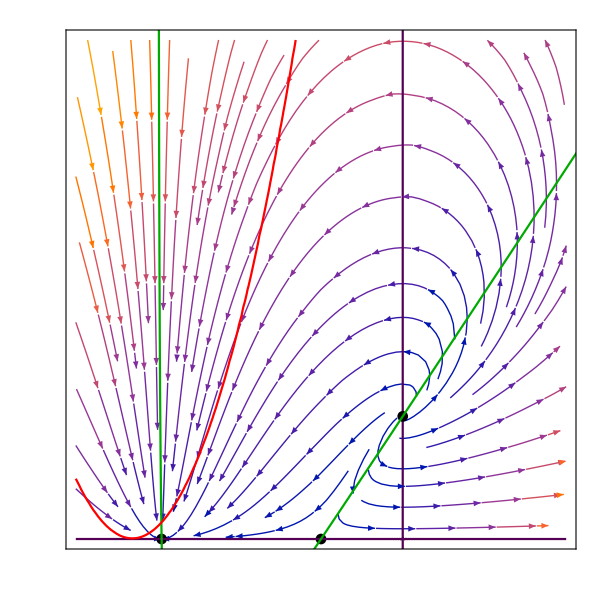

```mathematica
(*Show the plots of the phase space and fixed points together*)
Show[PhaseSpacexz,FPsxz,zLine,xLine,Accnxz,FrameLabel->{MaTeX["x",FontSize->18],MaTeX["z",FontSize->18]},FrameTicks->{{Table[{z,MaTeX[z,"DisplayStyle"->False,FontSize->18]},{z,0.5Range[-1,6]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->18]},{x,1Range[-1,5]}],None}},BaseStyle->{FontFamily->"CMU Serif",FontSize->20},PlotRange->{{-1,5},{0,3}},ImageSize->{600,600},PlotRangePadding->{0.08,0.08}]
```

### Non-Compact x - y - z Phase Space

```mathematica
(*Set parameter values such that a spiral repellor fixed point exists*)
wx=-0.5;
q=1;
ϵ=-0.25;
ℛ=0.05;
```

```mathematica
(*Define the dynamical system for interacting dark energy with a quadratic equation of state, x, dark matter, z, and the Hubble parameter, y*)
dex:=x'=-3*y*(x-ℛ)*(1+wx+ϵ*x)-q*x*y*z
dey:=y'=-y^2-(1/6)*(z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2) 
dez:=z'=-3*y*z + q*x*y*z
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{dex==0,dey==0,dez==0},{x,y,z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0.,z→0.0125 (6.+37. x+60. x^2)},{x→0.05,y→-0.129099,z→0.},{x→0.05,y→0.129099,z→0.},{x→2.,y→-0.816497,z→0.},{x→2.,y→0.816497,z→0.},{x→3.,y→-1.11617,z→0.7375},{x→3.,y→1.11617,z→0.7375}}

```mathematica
(*Extract the values for the fixed points and put them into a common variable name*)
FP[1]={x,y/.FPs[[1,1]],z/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],y/.FPs[[2,2]],z/.FPs[[2,3]]};
FP[3]={x/.FPs[[3,1]],y/.FPs[[3,2]],z/.FPs[[3,3]]};
FP[4]={x/.FPs[[4,1]],y/.FPs[[4,2]],z/.FPs[[4,3]]};
FP[5]={x/.FPs[[5,1]],y/.FPs[[5,2]],z/.FPs[[5,3]]};
FP[6]={x/.FPs[[6,1]],y/.FPs[[6,2]],z/.FPs[[6,3]]};
FP[7]={x/.FPs[[7,1]],y/.FPs[[7,2]],z/.FPs[[7,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPs=Table[FP[i],{i,1,7}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
Jxyz=Simplify[{{D[dex,x],D[dex,y],D[dex,z]}, {D[dey,x],D[dey,y],D[dey,z]},{D[dez,x],D[dez,y],D[dez,z]}}];
Jxyz//MatrixForm
```

(y (-1.5375+1.5 x-1. z) | 0.075+0.75 x^2-1. x (1.5375+z) | -x y
0.0770833+0.25 x | -2 y | -1/6
y z | (-3+x) z | (-3+x) y)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[Jxyz/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvalues[Jxyz/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm,Eigenvectors[Jxyz/.{x->FPs[[i,1]],y->FPs[[i,2]],z->FPs[[i,3]]}]//MatrixForm},{i,1,7}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(x
0.
0.0125 (6.+37. x+60. x^2)) | (0. | 0.075-1.6125 x+0.2875 x^2-0.75 x^3 | 0.
0.0770833+0.25 x | 0. | -1/6
0. | -0.225-1.3125 x-1.7875 x^2+0.75 x^3 | 0.) | (0
-√(0.0432812+0.113203 x-0.0830469 x^2-0.110937 x^3-0.1875 x^4)
√(0.0432812+0.113203 x-0.0830469 x^2-0.110937 x^3-0.1875 x^4)) | (0.666667/(0.308333+1. x) | 0 | 1.
-(1. (-0.0308333+0.562917 x+2.03181 x^2-0.075 x^3+1. x^4))/((0.308333+1. x) (-0.3-1.75 x-2.38333 x^2+1. x^3)) | -(1.33333 √(0.0432813+0.113203 x-0.0830469 x^2-0.110938 x^3-0.1875 x^4))/(-0.3-1.75 x-2.38333 x^2+1. x^3) | 1.
-(1. (-0.0308333+0.562917 x+2.03181 x^2-0.075 x^3+1. x^4))/((0.308333+1. x) (-0.3-1.75 x-2.38333 x^2+1. x^3)) | (1.33333 √(0.0432813+0.113203 x-0.0830469 x^2-0.110938 x^3-0.1875 x^4))/(-0.3-1.75 x-2.38333 x^2+1. x^3) | 1.)
(0.05
-0.129099
0.) | (0.188808 | 0. | 0.00645497
0.0895833 | 0.258199 | -1/6
0. | 0. | 0.380843) | (0.380843
0.258199
0.188808) | (0.0201538 | -0.800065 | 0.599574
0. | 1. | 0.
0.612372 | -0.790569 | 0.)
(0.05
0.129099
0.) | (-0.188808 | 0. | -0.00645497
0.0895833 | -0.258199 | -1/6
0. | 0. | -0.380843) | (-0.380843
-0.258199
-0.188808) | (0.0201538 | 0.800065 | 0.599574
0. | 1. | 0.
0.612372 | 0.790569 | 0.)
(2.
-0.816497
0.) | (-1.19413 | 0. | 1.63299
0.577083 | 1.63299 | -1/6
0. | 0. | 0.816497) | (1.63299
-1.19413
0.816497) | (0. | 1. | 0.
0.979796 | -0.2 | 0.
0.605959 | -0.275985 | 0.746087)
(2.
0.816497
0.) | (1.19413 | 0. | -1.63299
0.577083 | -1.63299 | -1/6
0. | 0. | -0.816497) | (-1.63299
1.19413
-0.816497) | (0. | 1. | 0.
0.979796 | 0.2 | 0.
0.605959 | 0.275985 | 0.746087)
(3.
-1.11617
0.7375) | (-2.48348 | -8.88178×10^-16 | 3.34851
0.827083 | 2.23234 | -1/6
-0.823175 | 0. | 0.) | (2.23234+0. ⅈ
-1.24174+1.10204 ⅈ
-1.24174-1.10204 ⅈ) | (-8.17767×10^-17+0. ⅈ | 1.+0. ⅈ | 1.5283×10^-16+0. ⅈ
0.880401+0. ⅈ | -0.180212-0.0432659 ⅈ | 0.326482+0.289752 ⅈ
0.880401+0. ⅈ | -0.180212+0.0432659 ⅈ | 0.326482-0.289752 ⅈ)
(3.
1.11617
0.7375) | (2.48348 | -8.88178×10^-16 | -3.34851
0.827083 | -2.23234 | -1/6
0.823175 | 0. | 0.) | (-2.23234+0. ⅈ
1.24174+1.10204 ⅈ
1.24174-1.10204 ⅈ) | (-8.17767×10^-17+0. ⅈ | -1.+0. ⅈ | 1.5283×10^-16+0. ⅈ
0.880401+0. ⅈ | 0.180212-0.0432659 ⅈ | 0.326482-0.289752 ⅈ
0.880401+0. ⅈ | 0.180212+0.0432659 ⅈ | 0.326482+0.289752 ⅈ)

```mathematica
(*Plot the line of Einstein fixed points*)
EinsteinPointLine=ParametricPlot3D[{FP[1][[1]],FP[1][[2]],FP[1][[3]]},{x,0,15},PlotStyle->Red];
```

```mathematica
(*Plot the fixed points of the system*)
FPsxyz=ListPointPlot3D[Table[FP[i],{i,2,7}],PlotStyle->Black];
```

```mathematica
Accnxyz=ContourPlot3D[z+x*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x^2==0,{x,0,12},{y,-10,10},{z,0,12},ContourStyle->{Red,Opacity[0.25]},Mesh->None];
```

```mathematica
(*Plot the x-y-z phase space*)
PhaseSpacexyz=StreamPlot3D[{dex,dey,dez},{x,0,15},{y,-5,5},{z,0,10},AxesLabel->{"x","y","z"}];
```

```mathematica
(*Show the phase space and the fixed points together*)
Show[PhaseSpacexyz,FPsxyz,EinsteinPointLine,Accnxyz]
```

-Graphics3D-

## Plot the constant x0 and z0 surfaces

### Set-up for the x-y-z phase spaces

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ**)

x0=ℛ/α;
y0=Sqrt[x0/3+z0/3-K];
```

```mathematica
(*Define K using the range of Ωk0 allowed by Planck 2018*)
Ωk0Open=0.003;
Ωk0Closed=-0.001;

KDensityParametersOpen=-Ωk0Open*ℛ/(3*α*Ωx0)
KDensityParametersClosed=-Ωk0Closed*ℛ/(3*α*Ωx0)
```

-0.000145159

0.0000483863

### Limiting Case with 1 Einstein fixed point

#### Find the Einstein Fixed Point

```mathematica
(*Fix z0 so that there is one Einstein fixed point on the surface*)
z0Limiting=0.007;
```

```mathematica
(*Substitute z0Limiting into y0 for this case*)
y0Limiting=y0/.z0->z0Limiting
```

√(0.0356667-K)

```mathematica
(*Define the system of differential equations for the dark energy, x, and dark matter, z*)
dext:=x1'[t]==-3*y1[t]*(x1[t]-ℛ)*(1+wx+ϵ*x1[t])-q*x1[t]*y1[t]*z1[t]
deyt:=y1'[t]==-y1[t]^2-(1/6)*(z1[t]+x1[t]*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x1[t]^2) 
dezt:=z1'[t]==-3*y1[t]*z1[t] + q*x1[t]*y1[t]*z1[t]
```

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajLimiting[K_]=NDSolve[{dext,deyt,dezt,x1[0]==x0,y1[0]==y0Limiting,z1[0]==z0Limiting},{x1,y1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition √(0.0356667-1. K) is not a number or a rectangular array of numbers.

NDSolve[{x1'[t]==-3 (0.5-0.25 x1[t]) (-0.05+x1[t]) y1[t]-x1[t] y1[t] z1[t],y1'[t]==-y1[t]^2+1/6 (0.075+0.4625 x1[t]+0.75 x1[t]^2-z1[t]),z1'[t]==-3 y1[t] z1[t]+x1[t] y1[t] z1[t],x1[0]==0.1,y1[0]==√(0.0356667-K),z1[0]==0.007},{x1,y1,z1},{t,-100,100}]

```mathematica
(*Table of all x1 and z1 values for each solution for each value of t*)
xTableSolLimiting=Table[x1[i]/.trajLimiting[0],{i,-100,100,.01}];
yTableSolLimiting=Table[y1[i]/.trajLimiting[0],{i,-100,100,.01}];
zTableSolLimiting=Table[z1[i]/.trajLimiting[0],{i,-100,100,.01}];
```

```mathematica
(*Using the values of x and z found numerically, solve the equation to find the Einstein fixed points*)
EinsteinPlotValuesSolLimiting=(zTableSolLimiting)+(xTableSolLimiting)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolLimiting)^2;
```

```mathematica
NearestToZeroLimiting=Flatten[Nearest[EinsteinPlotValuesSolLimiting,0]]
```

{-0.00951799}

```mathematica
PositionNearestToZeroLimiting=Flatten[Position[EinsteinPlotValuesSolLimiting,NearestToZeroLimiting]]
```

{9448}

```mathematica
EinsteinPointLimiting=Flatten[{xTableSolLimiting[[PositionNearestToZeroLimiting]],0,zTableSolLimiting[[PositionNearestToZeroLimiting]]}]
```

{0.6893,0,0.740634}

```mathematica
(*Find the Jacobian and eigenvalues for the Einstein fixed point*)
EinsteinTableLimiting=Table[{EinsteinPointLimiting//MatrixForm,Simplify[Jxyz/.{x->EinsteinPointLimiting[[1]],y->EinsteinPointLimiting[[2]],z->EinsteinPointLimiting[[3]]}]//MatrixForm,Eigenvalues[Jxyz/.{x->EinsteinPointLimiting[[1]],y->EinsteinPointLimiting[[2]],z->EinsteinPointLimiting[[3]]}]//MatrixForm,Eigenvectors[Jxyz/.{x->EinsteinPointLimiting[[1]],y->EinsteinPointLimiting[[2]],z->EinsteinPointLimiting[[3]]}]//MatrixForm},1];
```

```mathematica
(*Use TableForm to display the Einstein fixed point with their Jacobian matrix and eigenvalues*)
FPTableEinsteinPointLimiting=TableForm[EinsteinTableLimiting,TableHeadings->{None,{"Einstein Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Einstein Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.6893
0
0.740634) | (0. | -1.13897 | 0.
0.249408 | 0 | -1/6
0. | -1.71138 | 0.) | (-0.0340995
0.0340995
3.30671×10^-14) | (-0.553965 | -0.0165851 | -0.832375
0.553965 | -0.0165851 | 0.832375
0.55561 | -1.60851×10^-14 | 0.831443)

```mathematica
(*Table of all x1 and z1 values for each solution for each value of t*)
xTableSolLimitingFull=Table[x1[i]/.trajLimiting[0],{i,-100,100,.1}];
yTableSolLimitingFull=Table[y1[i]/.trajLimiting[0],{i,-100,100,.1}];
zTableSolLimitingFull=Table[z1[i]/.trajLimiting[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the equation to find the Einstein fixed points*)
EinsteinPlotValuesSolLimitingFull=(zTableSolLimitingFull)+(xTableSolLimitingFull)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolLimitingFull)^2;
```

```mathematica
(*Merge the xTable values and the EinsteinPlotValueSol values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsLimiting=MapThread[h,{xTableSolLimitingFull,EinsteinPlotValuesSolLimitingFull}];
```

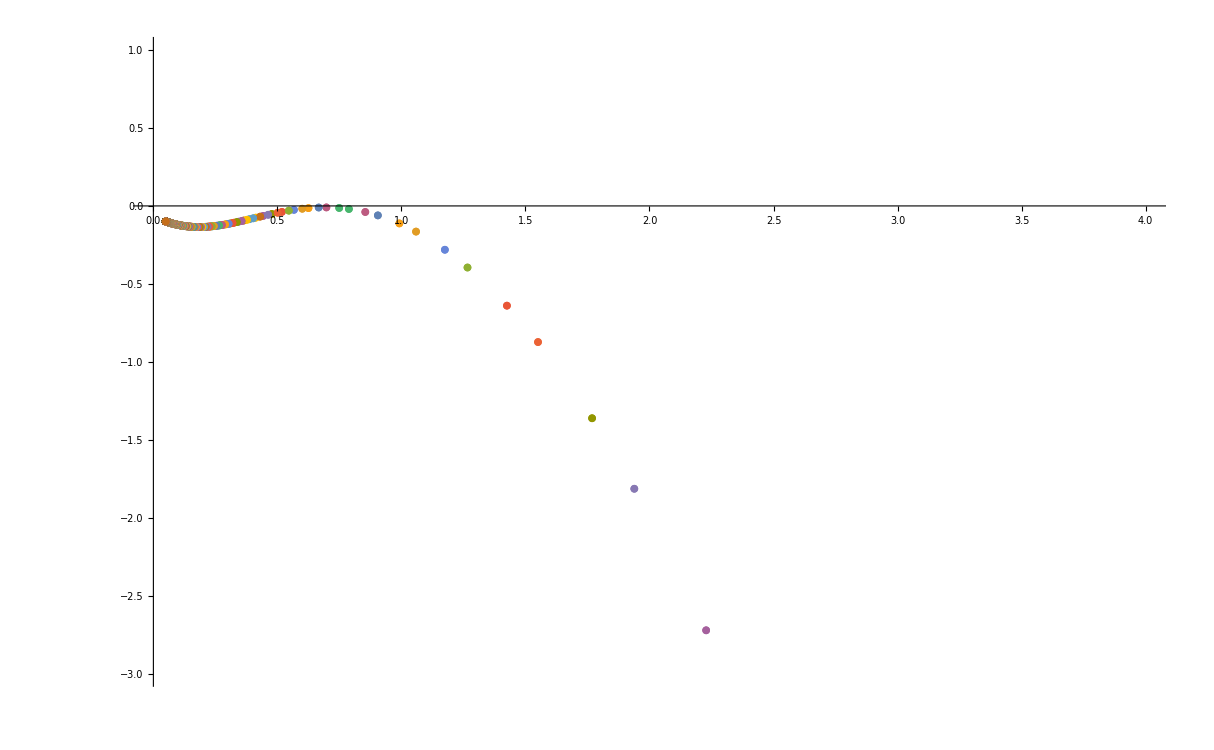

```mathematica
(*Plot each solution for each initial condition*)
EinsteinPlotLimiting=ListPlot[EinsteinPointSolutionsLimiting,PlotRange->{{0,4},{-3,1}}]
```

#### Plot the x-y-z Phase Space

```mathematica
KMaxLimiting=K/.Solve[y0Limiting==0,K]
```

{0.0356667}

```mathematica
solLimiting[1]=trajLimiting[KDensityParametersOpen]
solLimiting[2]=trajLimiting[KDensityParametersClosed]
solLimiting[3]=trajLimiting[-.1]
solLimiting[4]=trajLimiting[0.04]
solLimiting[5]=trajLimiting[0.005]
```

NDSolve::ndsz: At t == -8.59273, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

NDSolve::ndsz: At t == -2.88294, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
trajLimitingxyz[1]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimiting[1],{t,-8.58,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingxyz[2]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimiting[2],{t,-100,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingxyz[3]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimiting[3],{t,-2.87,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingxyz[4]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimiting[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingxyz[5]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solLimiting[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCase=Table[trajLimitingxyz[i],{i,1,5}];
```

```mathematica
EinsteinFixedPointsLimiting=ListPointPlot3D[{EinsteinPointLimiting},PlotStyle->Black];
```

```mathematica
CFSLimitingSol=NDSolve[{dext,deyt,dezt,x1[0]==EinsteinPointLimiting[[1]],y1[0]==0,z1[0]==EinsteinPointLimiting[[3]]},{x1,y1,z1},{t,-100,100}]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
CFSLimiting=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.CFSLimitingSol,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
FFSLimitingSol=trajLimiting[0]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
FFSLimiting=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.FFSLimitingSol,{t,-10,100},PlotStyle -> {{Darker[Green],Thick}}],PlotPoints->500,PlotRange->{{0,6},{-3,3},{0,6}}];
```

```mathematica
Show[trajLimitingCase,EinsteinFixedPointsLimiting,CFSLimiting,FFSLimiting,Accnxyz,FPsxyz,PlotRange->{{0.05,5},{-5,5},{0,3}},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

#### Plot the x-z Projection

```mathematica
trajLimitingxz=ParametricPlot[Evaluate[{{x1[t],z1[t]}}/.solLimiting[1],{t,-8.58,100},PlotStyle -> {{Black, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
EinsteinFixedPointsLimitingxz=ListPlot[{{EinsteinPointLimiting[[1]],EinsteinPointLimiting[[3]]}},PlotStyle->Black];
```

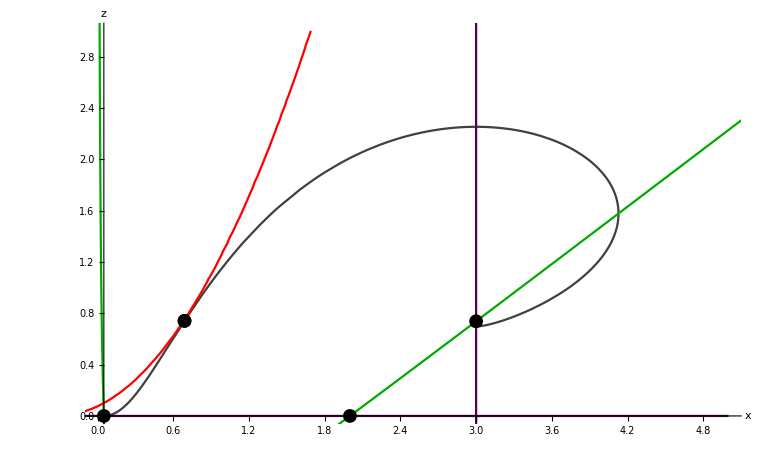

```mathematica
Show[trajLimitingxz,xLine,zLine,Accnxz,FPsxz,EinsteinFixedPointsLimitingxz,PlotRange->{{0,5},{0,3}},AxesLabel->{"x","z"}]
```

### Two Einstein Fixed Points

#### Find the Einstein Fixed Points

```mathematica
(*Fix z0 using the density parameters*)
z0TwoEinsteinPoints=Ωm0*ℛ/(Ωx0*α);
```

```mathematica
(*Substitute z0TwoEinsteinPoints into y0 for this case*)
y0TwoEinsteinPoints=y0/.z0->z0TwoEinsteinPoints
```

√(0.0483863-K)

```mathematica
(*Define the system of differential equations for the dark energy, x, and dark matter, z*)
dext:=x1'[t]==-3*y1[t]*(x1[t]-ℛ)*(1+wx+ϵ*x1[t])-q*x1[t]*y1[t]*z1[t]
deyt:=y1'[t]==-y1[t]^2-(1/6)*(z1[t]+x1[t]*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x1[t]^2) 
dezt:=z1'[t]==-3*y1[t]*z1[t] + q*x1[t]*y1[t]*z1[t]
```

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajTwoEinsteinPoints[K_]=NDSolve[{dext,deyt,dezt,x1[0]==x0,y1[0]==y0TwoEinsteinPoints,z1[0]==z0TwoEinsteinPoints},{x1,y1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition √(0.0483863-1. K) is not a number or a rectangular array of numbers.

NDSolve[{x1'[t]==-3 (0.5-0.25 x1[t]) (-0.05+x1[t]) y1[t]-x1[t] y1[t] z1[t],y1'[t]==-y1[t]^2+1/6 (0.075+0.4625 x1[t]+0.75 x1[t]^2-z1[t]),z1'[t]==-3 y1[t] z1[t]+x1[t] y1[t] z1[t],x1[0]==0.1,y1[0]==√(0.0483863-K),z1[0]==0.0451589},{x1,y1,z1},{t,-100,100}]

```mathematica
xTableSol1TwoEinsteinPoints=Table[x1[i]/.trajTwoEinsteinPoints[0],{i,-2,100,.01}];
yTableSol1TwoEinsteinPoints=Table[y1[i]/.trajTwoEinsteinPoints[0],{i,-2,100,.01}];
zTableSol1TwoEinsteinPoints=Table[z1[i]/.trajTwoEinsteinPoints[0],{i,-2,100,.01}];
```

```mathematica
(*Using the values of x and z found numerically, solve the equation to find the Einstein fixed points*)
EinsteinPlotValuesSol1TwoEinsteinPoints=(zTableSol1TwoEinsteinPoints)+(xTableSol1TwoEinsteinPoints)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol1TwoEinsteinPoints)^2;
```

```mathematica
NearestToZeroTwoEinsteinPoints1=Flatten[Nearest[EinsteinPlotValuesSol1TwoEinsteinPoints,0]]
```

{0.000215008}

```mathematica
PositionNearestToZeroTwoEinsteinPoints1=Flatten[Position[EinsteinPlotValuesSol1TwoEinsteinPoints,NearestToZeroTwoEinsteinPoints1]]
```

{32}

```mathematica
EinsteinPoint1TwoEinsteinPoints=Flatten[{xTableSol1TwoEinsteinPoints[[PositionNearestToZeroTwoEinsteinPoints1]],0,zTableSol1TwoEinsteinPoints[[PositionNearestToZeroTwoEinsteinPoints1]]}]
```

{0.149763,0,0.161302}

```mathematica
(*Table of all x1 and z1 values for each solution for each value of t*)
xTableSol2TwoEinsteinPoints=Table[x1[i]/.trajTwoEinsteinPoints[0],{i,-5.6,-3.2,.001}];
yTableSol2TwoEinsteinPoints=Table[y1[i]/.trajTwoEinsteinPoints[0],{i,-5.6,-3.2,.001}];
zTableSol2TwoEinsteinPoints=Table[z1[i]/.trajTwoEinsteinPoints[0],{i,-5.6,-3.2,.001}];
```

```mathematica
(*Using the values of x and z found numerically, solve the equation to find the Einstein fixed points*)
EinsteinPlotValuesSol2TwoEinsteinPoints=(zTableSol2TwoEinsteinPoints)+(xTableSol2TwoEinsteinPoints)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSol2TwoEinsteinPoints)^2;
```

```mathematica
NearestToZeroTwoEinsteinPoints2=Flatten[Nearest[EinsteinPlotValuesSol2TwoEinsteinPoints,0]]
```

{0.00310612}

```mathematica
PositionNearestToZeroTwoEinsteinPoints2=Flatten[Position[EinsteinPlotValuesSol2TwoEinsteinPoints,NearestToZeroTwoEinsteinPoints2]]
```

{1876}

```mathematica
EinsteinPoint2TwoEinsteinPoints=Flatten[{xTableSol2TwoEinsteinPoints[[PositionNearestToZeroTwoEinsteinPoints2]],0,zTableSol2TwoEinsteinPoints[[PositionNearestToZeroTwoEinsteinPoints2]]}]
```

{1.727,0,3.11374}

```mathematica
(*Put the Einstein fixed points into a common variable name*)
EinsteinPointTwoEPts[1]=EinsteinPoint1TwoEinsteinPoints;
EinsteinPointTwoEPts[2]=EinsteinPoint2TwoEinsteinPoints;
```

```mathematica
(*Put the Einstein fixed points into a table*)
EinsteinPointsTwoEPts=Table[EinsteinPointTwoEPts[i],{i,1,2}];
```

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
EinsteinPointTableTwoEinsteinPoints=Table[{EinsteinPointsTwoEPts[[i]]//MatrixForm,Simplify[Jxyz/.{x->EinsteinPointsTwoEPts[[i,1]],y->EinsteinPointsTwoEPts[[i,2]],z->EinsteinPointsTwoEPts[[i,3]]}]//MatrixForm,Eigenvalues[Jxyz/.{x->EinsteinPointsTwoEPts[[i,1]],y->EinsteinPointsTwoEPts[[i,2]],z->EinsteinPointsTwoEPts[[i,3]]}]//MatrixForm,Eigenvectors[Jxyz/.{x->EinsteinPointsTwoEPts[[i,1]],y->EinsteinPointsTwoEPts[[i,2]],z->EinsteinPointsTwoEPts[[i,3]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTableTwoEinsteinPoints=TableForm[EinsteinPointTableTwoEinsteinPoints,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.149763
0
0.161302) | (0. | -0.162596 | 0.
0.114524 | 0 | -1/6
0. | -0.459749 | 0.) | (0.24084
-0.24084
8.53342×10^-18) | (0.298953 | -0.442814 | 0.845306
-0.298953 | -0.442814 | -0.845306
0.824179 | 1.47427×10^-16 | 0.56633)
(1.727
0
3.11374) | (0. | -5.7208 | 0.
0.508834 | 0 | -1/6
0. | -3.96379 | 0.) | (-1.33922×10^-16+1.5001 ⅈ
-1.33922×10^-16-1.5001 ⅈ
1.11057×10^-16+0. ⅈ) | (0.803522+0. ⅈ | 9.39819×10^-17-0.210699 ⅈ | 0.556739-2.03432×10^-16 ⅈ
0.803522+0. ⅈ | 9.39819×10^-17+0.210699 ⅈ | 0.556739+2.03432×10^-16 ⅈ
0.311274+0. ⅈ | 9.05767×10^-17+0. ⅈ | 0.95032+0. ⅈ)

```mathematica
(*Table of all x1 and z1 values for each solution for each value of t*)
xTableSolTwoEinsteinPointsFull=Table[x1[i]/.trajTwoEinsteinPoints[0],{i,-100,100,.1}];
yTableSolTwoEinsteinPointsFull=Table[y1[i]/.trajTwoEinsteinPoints[0],{i,-100,100,.1}];
zTableSolTwoEinsteinPointsFull=Table[z1[i]/.trajTwoEinsteinPoints[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the equation to find the Einstein fixed points*)
EinsteinPlotValuesSolTwoEinsteinPointsFull=(zTableSolTwoEinsteinPointsFull)+(xTableSolTwoEinsteinPointsFull)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolTwoEinsteinPointsFull)^2;
```

```mathematica
(*Merge the xTable values and the EinsteinPlotValueSol values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsTwoEinsteinPoints=MapThread[h,{xTableSolTwoEinsteinPointsFull,EinsteinPlotValuesSolTwoEinsteinPointsFull}];
```

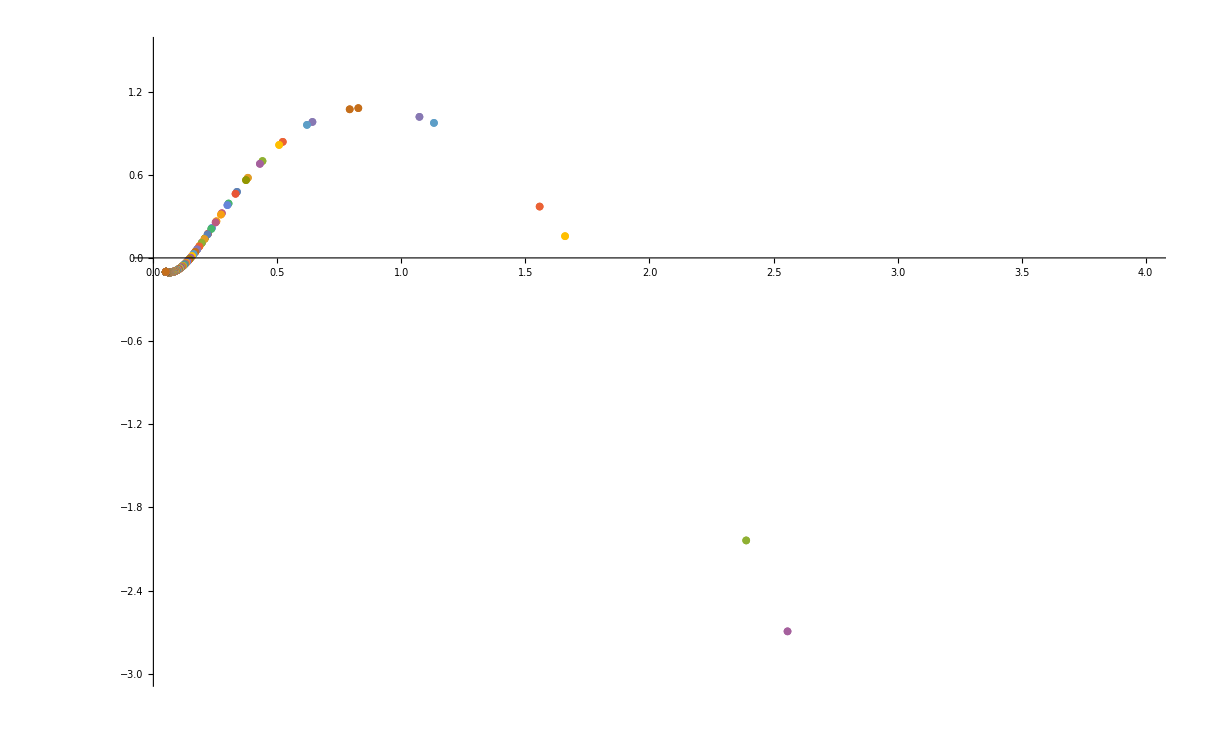

```mathematica
(*Plot each solution for each initial condition*)
EinsteinPlotTwoEinsteinPoints=ListPlot[EinsteinPointSolutionsTwoEinsteinPoints,PlotRange->{{0,4},{-3,1.5}}]
```

#### Plot the x-y-z Phase Space

```mathematica
(*Find the maximum value of K so that y0 is not imaginary*)
KMaxTwoEinsteinPoints=K/.Flatten[Solve[y0TwoEinsteinPoints==0,K]]
```

0.0483863

```mathematica
solTwoEinsteinPoints[1]=trajTwoEinsteinPoints[KDensityParametersOpen]
```

NDSolve::ndsz: At t == -6.68211, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPoints[2]=trajTwoEinsteinPoints[KDensityParametersClosed]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPoints[3]=trajTwoEinsteinPoints[-.1]
```

NDSolve::ndsz: At t == -2.6552, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPoints[4]=trajTwoEinsteinPoints[KMaxTwoEinsteinPoints]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPoints[5]=trajTwoEinsteinPoints[0.005]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
trajTwoEinsteinPointsxyz[1]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPoints[1],{t,-6.67,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyz[2]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPoints[2],{t,-100,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyz[3]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPoints[3],{t,-2.65,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsxyz[4]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPoints[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75],Dashed}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
trajTwoEinsteinPointsxyz[5]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solTwoEinsteinPoints[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsCase=Table[trajTwoEinsteinPointsxyz[i],{i,1,5}];
```

```mathematica
EinsteinFixedPointsTwoEinsteinPoints=ListPointPlot3D[{EinsteinPoint1TwoEinsteinPoints,EinsteinPoint2TwoEinsteinPoints},PlotStyle->Black];
```

```mathematica
CFSTwoEinsteinPointsSol=NDSolve[{dext,deyt,dezt,x1[0]==EinsteinPoint1TwoEinsteinPoints[[1]],y1[0]==-0.0005,z1[0]==EinsteinPoint1TwoEinsteinPoints[[3]]},{x1,y1,z1},{t,-100,100}]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
CFSTwoEinsteinPoints=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.CFSTwoEinsteinPointsSol,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->All];
```

```mathematica
FFSTwoEinsteinPointsSol=trajTwoEinsteinPoints[0]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
FFSTwoEinsteinPoints=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.FFSTwoEinsteinPointsSol,{t,-8,100},PlotStyle -> {{Darker[Green],Thick}}],PlotPoints->500,PlotRange->{{0,6},{-3,3},{0,6}}];
```

```mathematica
Show[trajTwoEinsteinPointsCase,CFSTwoEinsteinPoints,EinsteinFixedPointsTwoEinsteinPoints,Accnxyz,FFSTwoEinsteinPoints,FPsxyz,PlotRange->{{0.05,5},{-5,5},{0,4}},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

#### Plot the x-z Projection

```mathematica
trajTwoEinsteinPointsxz=ParametricPlot[Evaluate[{{x1[t],z1[t]}}/.solTwoEinsteinPoints[1],{t,-6.67,100},PlotStyle -> {{Black, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
EinsteinFixedPointsTwoEinsteinPointsxz=ListPlot[{{EinsteinPoint1TwoEinsteinPoints[[1]],EinsteinPoint1TwoEinsteinPoints[[3]]},{EinsteinPoint2TwoEinsteinPoints[[1]],EinsteinPoint2TwoEinsteinPoints[[3]]}},PlotStyle->Black];
```

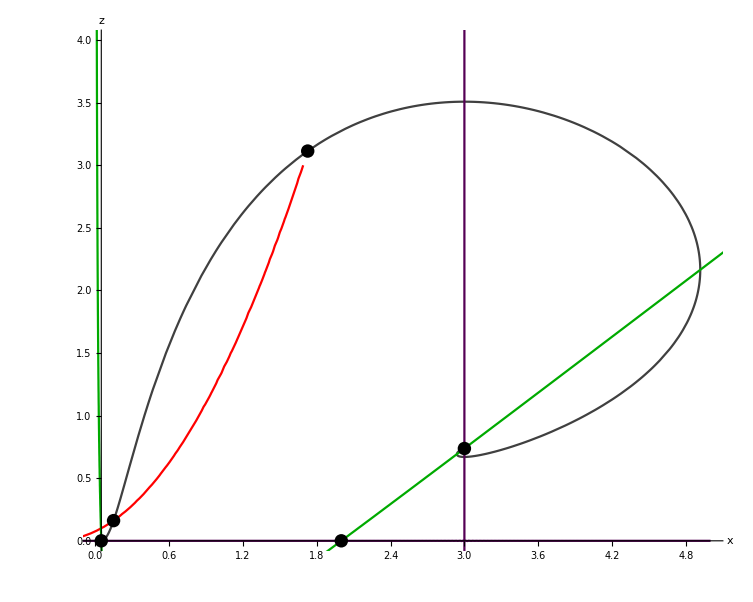

```mathematica
Show[trajTwoEinsteinPointsxz,Accnxz,xLine,zLine,FPsxz,EinsteinFixedPointsTwoEinsteinPointsxz,PlotRange->{{0,5},{0,4}},AxesLabel->{"x","z"}]
```

### No Einstein Fixed Points

#### Plot to show that there are no Einstein fixed points

```mathematica
(*Fix z0 such that there are no Einstein fixed points on the surface*)
z0NoEinsteinPoints=0.005;
```

```mathematica
(*Substitute z0NoEinsteinPoints into y0 for this case*)
y0NoEinsteinPoints=y0/.z0->z0NoEinsteinPoints
```

√(0.035-K)

```mathematica
(*Define the system of differential equations for the dark energy, x, and dark matter, z*)
dext:=x1'[t]==-3*y1[t]*(x1[t]-ℛ)*(1+wx+ϵ*x1[t])-q*x1[t]*y1[t]*z1[t]
deyt:=y1'[t]==-y1[t]^2-(1/6)*(z1[t]+x1[t]*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*x1[t]^2) 
dezt:=z1'[t]==-3*y1[t]*z1[t] + q*x1[t]*y1[t]*z1[t]
```

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajNoEinsteinPoints[K_]=NDSolve[{dext,deyt,dezt,x1[0]==x0,y1[0]==y0NoEinsteinPoints,z1[0]==z0NoEinsteinPoints},{x1,y1,z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition √(0.035-1. K) is not a number or a rectangular array of numbers.

NDSolve[{x1'[t]==-3 (0.5-0.25 x1[t]) (-0.05+x1[t]) y1[t]-x1[t] y1[t] z1[t],y1'[t]==-y1[t]^2+1/6 (0.075+0.4625 x1[t]+0.75 x1[t]^2-z1[t]),z1'[t]==-3 y1[t] z1[t]+x1[t] y1[t] z1[t],x1[0]==0.1,y1[0]==√(0.035-K),z1[0]==0.005},{x1,y1,z1},{t,-100,100}]

```mathematica
(*Table of all x1 and z1 values for each solution for each value of t*)
xTableSolNoEinsteinPointsFull=Table[x1[i]/.trajNoEinsteinPoints[0],{i,-100,100,.1}];
yTableSolNoEinsteinPointsFull=Table[y1[i]/.trajNoEinsteinPoints[0],{i,-100,100,.1}];
zTableSolNoEinsteinPointsFull=Table[z1[i]/.trajNoEinsteinPoints[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the equation to find the Einstein fixed points*)
EinsteinPlotValuesSolNoEinsteinPointsFull=(zTableSolNoEinsteinPointsFull)+(xTableSolNoEinsteinPointsFull)*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(xTableSolNoEinsteinPointsFull)^2;
```

```mathematica
(*Merge the xTable values and the EinsteinPlotValueSol values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsNoEinsteinPoints=MapThread[h,{xTableSolNoEinsteinPointsFull,EinsteinPlotValuesSolNoEinsteinPointsFull}];
```

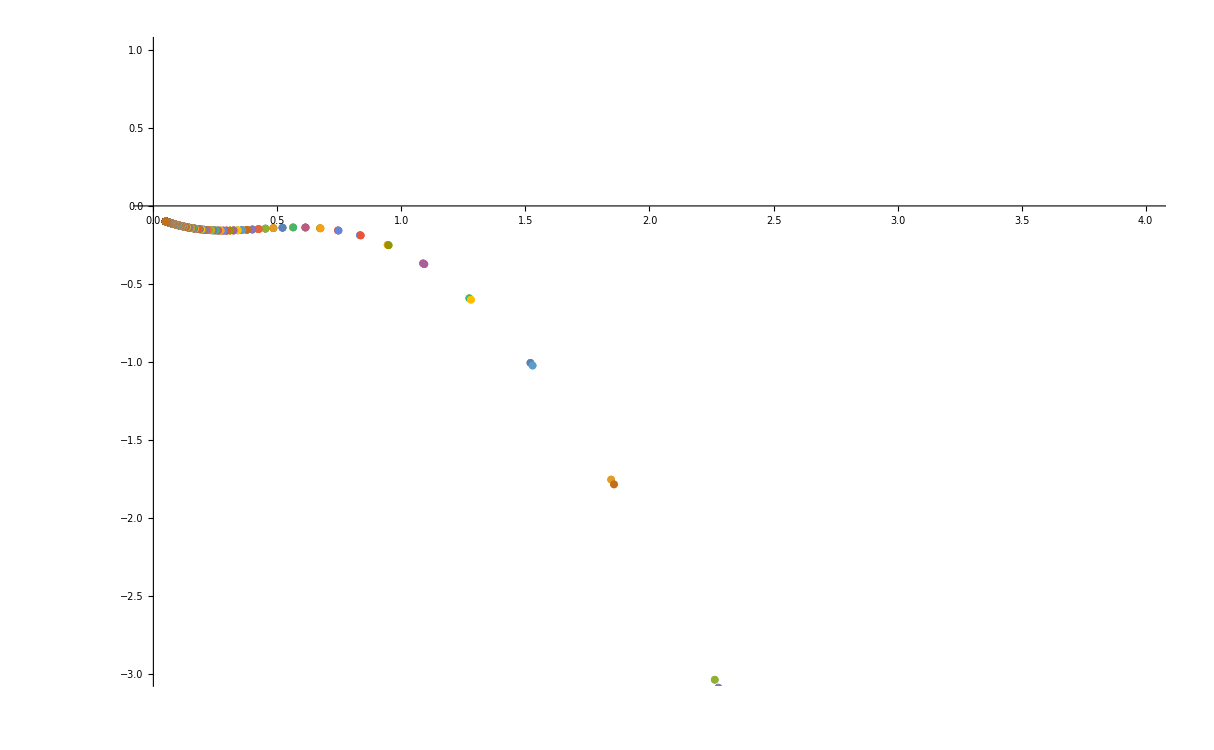

```mathematica
(*Plot each solution for each initial condition*)
EinsteinPlotNoEinsteinPoints=ListPlot[EinsteinPointSolutionsNoEinsteinPoints,PlotRange->{{0,4},{-3,1}}]
```

#### Plot the x-y-z Phase Space

```mathematica
KMaxNoEinsteinPoints=K/.Solve[y0NoEinsteinPoints==0,K][[1]]
```

0.035

```mathematica
solNoEinsteinPoints[1]=trajNoEinsteinPoints[KDensityParametersOpen]
solNoEinsteinPoints[2]=trajNoEinsteinPoints[KDensityParametersClosed]
solNoEinsteinPoints[3]=trajNoEinsteinPoints[-.1]
solNoEinsteinPoints[4]=trajNoEinsteinPoints[0.01]
solNoEinsteinPoints[5]=trajNoEinsteinPoints[KMaxNoEinsteinPoints]
```

NDSolve::ndsz: At t == -8.89261, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

NDSolve::ndsz: At t == -2.89968, step size is effectively zero; singularity or stiff system suspected.

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
trajNoEinsteinPointsxyz[1]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPoints[1],{t,-8.89,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyz[2]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPoints[2],{t,-100,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyz[3]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPoints[3],{t,-2.89,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyz[4]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPoints[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsxyz[5]=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.solNoEinsteinPoints[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsPlots=Table[trajNoEinsteinPointsxyz[i],{i,1,5}];
```

```mathematica
FFSNoEinsteinPointsSol=trajNoEinsteinPoints[0]
```

{{x1→InterpolatingFunction[…],y1→InterpolatingFunction[…],z1→InterpolatingFunction[…]}}

```mathematica
FFSNoEinsteinPoints=ParametricPlot3D[Evaluate[{{x1[t],y1[t],z1[t]},{x1[t],-y1[t],z1[t]}}/.FFSNoEinsteinPointsSol,{t,-10,100},PlotStyle -> {{Darker[Green],Thick}}],PlotPoints->500,PlotRange->{{0,6},{-3,3},{0,6}}];
```

```mathematica
Show[trajNoEinsteinPointsPlots,FFSNoEinsteinPoints,Accnxyz,FPsxyz,PlotRange->{{0.05,5},{-5,5},{0,4}},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

#### Plot the x-z Projection

```mathematica
trajNoEinsteinPointsxz=ParametricPlot[Evaluate[{{x1[t],z1[t]}}/.solNoEinsteinPoints[1],{t,-8.89,100},PlotStyle -> {{Black, Opacity[0.75]}}],PlotPoints->500];
```

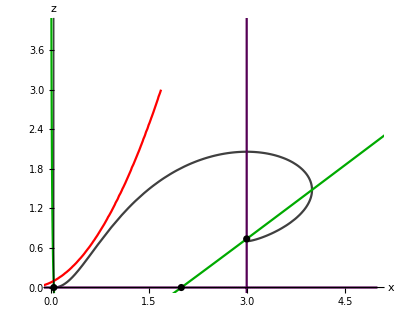

```mathematica
Show[trajNoEinsteinPointsxz,xLine,zLine,Accnxz,FPsxz,PlotRange->{{0,5},{0,4}},AxesLabel->{"x","z"}]
```

## Compact Phase Spaces: constant X0 and Z0 surfaces

### Define parameter values and set-up initial conditions

```mathematica
(*Parameter values are set such that a spiral repellor fixed point exists*)
wx=-0.5;
q=1;
ϵ=-0.25;
ℛ=0.05;
```

```mathematica
(*Define Ωx0 and Ωm0 using data from Planck 2018*)
Ωx0=0.6889;
Ωm0=0.3111;
```

```mathematica
(*Set a value for α, which sets the value of the low energy cosmological constant*)
α=0.5;
```

```mathematica
(*Define the initial conditions, where a0 = 1 and K is defined as k/ρ**)

x0=ℛ/α;
y0=Sqrt[x0/3+Z0/(3*(1-Z0))-K];
```

```mathematica
(*Compactify the initial conditions*)

X0=x0/(1+x0);
Y0=y0/Sqrt[1+y0^2];
```

```mathematica
(*Define K using the range of Ωk0 allowed by Planck 2018*)
Ωk0Open=0.003;
Ωk0Closed=-0.001;

KDensityParametersOpen=-Ωk0Open*ℛ/(3*α*Ωx0)
KDensityParametersClosed=-Ωk0Closed*ℛ/(3*α*Ωx0)
```

-0.000145159

0.0000483863

### Set-up for the compact X-Y-Z system

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y*)
deX:=X'=-3*(Y/((1-Y^2)^(1/2)))*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))*(Y/((1-Y^2)^(1/2)))
deY:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X^2/((1-X)^2))
deZ:=Z'=-3*Z*(1-Z)*(Y/((1-Y^2)^(1/2))) + q*(X/(1-X))*Z*(1-Z)*(Y/((1-Y^2)^(1/2)))
```

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y*)
deXt:=X1'[t]==-3*(Y1[t]/((1-Y1[t]^2)^(1/2)))*(X1[t]-ℛ*(1-X1[t]))*((1+wx)*(1-X1[t])+ϵ*X1[t])-q*X1[t]*(1-X1[t])*(Z1[t]/(1-Z1[t]))*(Y1[t]/((1-Y1[t]^2)^(1/2)))
deYt:=Y1'[t]==-Y1[t]^2*(1-Y1[t]^2)^(1/2)-(((1-Y1[t]^2)^(3/2))/6)*((Z1[t]/(1-Z1[t]))+(X1[t]/(1-X1[t]))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*X1[t]^2/((1-X1[t])^2))
deZt:=Z1'[t]==-3*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2))) + q*(X1[t]/(1-X1[t]))*Z1[t]*(1-Z1[t])*(Y1[t]/((1-Y1[t]^2)^(1/2)))
```

```mathematica
(*Find the fixed points of the system*)
FPsXYZ=Solve[{deX==0,deY==0,deZ==0},{X,Y,Z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Y→0.,Z→(6.+25. X+29. X^2)/(86.-135. X+109. X^2)},{X→0.666667,Y→-0.632456,Z→0.},{X→0.047619,Y→-0.128037,Z→0.},{X→-0.431034-0.145278 ⅈ,Y→0.,Z→0.},{X→-0.431034+0.145278 ⅈ,Y→0.,Z→0.},{X→0.047619,Y→0.128037,Z→0.},{X→0.666667,Y→0.632456,Z→0.},{X→0.75,Y→-0.744803,Z→0.42446},{X→0.75,Y→0.744803,Z→0.42446},{X→0.75,Y→0.,Z→0.891452}}

```mathematica
(*Extract the values of the fixed points and put them into a common variable name*)
FPXYZ[1]={X,Y/.FPsXYZ[[1,1]],Z/.FPsXYZ[[1,2]]};
FPXYZ[2]={X/.FPsXYZ[[2,1]],Y/.FPsXYZ[[2,2]],Z/.FPsXYZ[[2,3]]};
FPXYZ[3]={X/.FPsXYZ[[3,1]],Y/.FPsXYZ[[3,2]],Z/.FPsXYZ[[3,3]]};
FPXYZ[4]={X/.FPsXYZ[[6,1]],Y/.FPsXYZ[[6,2]],Z/.FPsXYZ[[6,3]]};
FPXYZ[5]={X/.FPsXYZ[[7,1]],Y/.FPsXYZ[[7,2]],Z/.FPsXYZ[[7,3]]};
FPXYZ[6]={X/.FPsXYZ[[8,1]],Y/.FPsXYZ[[8,2]],Z/.FPsXYZ[[8,3]]};
FPXYZ[7]={X/.FPsXYZ[[9,1]],Y/.FPsXYZ[[9,2]],Z/.FPsXYZ[[9,3]]};
FPXYZ[8]={X/.FPsXYZ[[10,1]],Y/.FPsXYZ[[10,2]],Z/.FPsXYZ[[10,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPXYZTable=Table[FPXYZ[i],{i,1,8}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
JCompactXYZ=Simplify[{{D[deX,X],D[deX,Y],D[deX,Z]},{D[deY,X],D[deY,Y],D[deY,Z]},{D[deZ,X],D[deZ,Y],D[deZ,Z]}}];
JCompactXYZ//MatrixForm
```

((Y (1.6875-0.6875 Z+X (-4.725+2.725 Z)))/(√(1-Y^2) (-1.+Z)) | (0.075+X^2 (2.3625-1.3625 Z)+X (-1.6875+0.6875 Z)-0.075 Z)/(√(1-Y^2) (-1.+Y^2) (-1.+Z)) | ((-1+X) X Y)/(√(1-Y^2) (-1+Z)^2)
(0.172917 (0.445783+1. X) √(1-Y^2) (-1.+Y^2))/(-1.+X)^3 | (Y (2.0375-2.5375 Z+Y^2 (-3.0375+3.5375 Z)+X (-3.84375+Y^2 (5.84375-6.84375 Z)+4.84375 Z)+X^2 (2.18125-2.68125 Z+Y^2 (-3.18125+3.68125 Z))))/((-1.+X)^2 √(1-Y^2) (-1.+Z)) | -((1-Y^2)^(3/2))/(6 (-1+Z)^2)
-(Y (-1+Z) Z)/((-1+X)^2 √(1-Y^2)) | ((-3+4 X) (-1+Z) Z)/((-1+X) (1-Y^2)^(3/2)) | ((-3+4 X) Y (-1+2 Z))/((-1+X) √(1-Y^2)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTableCompact=Table[{FPXYZTable[[i]]//MatrixForm,Simplify[JCompactXYZ/.{X->FPXYZTable[[i,1]],Y->FPXYZTable[[i,2]],Z->FPXYZTable[[i,3]]}]//MatrixForm,Eigenvalues[JCompactXYZ/.{X->FPXYZTable[[i,1]],Y->FPXYZTable[[i,2]],Z->FPXYZTable[[i,3]]}]//MatrixForm,Eigenvectors[JCompactXYZ/.{X->FPXYZTable[[i,1]],Y->FPXYZTable[[i,2]],Z->FPXYZTable[[i,3]]}]//MatrixForm},{i,1,8}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
(*Extra fixed points from compactification at {X = 1, Z = 0},{X = 1, Z = 1},{X = 0, Z = 1}*)
FPTableXYZ=TableForm[FPTableCompact,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(X
0.
(6.+25. X+29. X^2)/(86.-135. X+109. X^2)) | (0. | (0.075-1.9125 X+5.575 X^2-6.4625 X^3+2.725 X^4)/(1.-2. X+1. X^2) | 0.
(-0.0770833-0.172917 X)/(-1.+X)^3 | 0. | -(0.309401 (0.788991-1.23853 X+1. X^2)^2)/((1.-2. X+1. X^2)^2)
0. | (0.121202+0.101002 X-0.653144 X^2-0.262604 X^3+1.47462 X^4-0.781079 X^5)/((-1.+X) (0.788991-1.23853 X+1. X^2)^2) | 0.) | (0
-(√(2.36752×10^6-3.23487×10^7 X+2.03048×10^8 X^2-7.61682×10^8 X^3+1.80853×10^9 X^4-2.3693×10^9 X^5-5.96589×10^8 X^6+1.13797×10^10 X^7-3.17438×10^10 X^8+5.67742×10^10 X^9-7.55941×10^10 X^10+7.849×10^10 X^11-6.45121×10^10 X^12+4.19172×10^10 X^13-2.12178×10^10 X^14+8.11413×10^9 X^15-2.21527×10^9 X^16+3.86202×10^8 X^17-3.24002×10^7 X^18))/((-1.+X)^4 √(1.-2. X+1. X^2) (86.-135. X+109. X^2)^2)
(√(2.36752×10^6-3.23487×10^7 X+2.03048×10^8 X^2-7.61682×10^8 X^3+1.80853×10^9 X^4-2.3693×10^9 X^5-5.96589×10^8 X^6+1.13797×10^10 X^7-3.17438×10^10 X^8+5.67742×10^10 X^9-7.55941×10^10 X^10+7.849×10^10 X^11-6.45121×10^10 X^12+4.19172×10^10 X^13-2.12178×10^10 X^14+8.11413×10^9 X^15-2.21527×10^9 X^16+3.86202×10^8 X^17-3.24002×10^7 X^18))/((-1.+X)^4 √(1.-2. X+1. X^2) (86.-135. X+109. X^2)^2)) | (-(1.78931 (-1.+X)^3 (0.788991-1.23853 X+1. X^2)^2)/((0.445783+1. X) (1.-2. X+1. X^2)^2) | 0 | 1.
-(1. (-0.0165874+0.606034 X-6.81355 X^2+40.8788 X^3-153.503 X^4+370.935 X^5-488.211 X^6-216.371 X^7+2925.39 X^8-8444.38 X^9+15943.1 X^10-22619.1 X^11+25232.4 X^12-22502.4 X^13+16080.6 X^14-9133.98 X^15+4046.6 X^16-1351.95 X^17+321.135 X^18-48.4237 X^19+3.48876 X^20))/((-1.+1. X)^6 (-0.75+1. X) (0.445783+1. X) (1.-2. X+1. X^2)^2 (0.788991-1.23853 X+1. X^2)^2 (0.206897+0.862069 X+1. X^2)) | ((0.+4.20932×10^-7 ⅈ) √(-2.48252×10^12+3.39201×10^13 X-2.12911×10^14 X^2+7.98682×10^14 X^3-1.89638×10^15 X^4+2.48439×10^15 X^5+6.25569×10^14 X^6-1.19325×10^16 X^7+3.32858×10^16 X^8-5.95321×10^16 X^9+7.92661×10^16 X^10-8.23027×10^16 X^11+6.76458×10^16 X^12-4.39534×10^16 X^13+2.22485×10^16 X^14-8.50829×10^15 X^15+2.32288×10^15 X^16-4.04963×10^14 X^17+3.39741×10^13 X^18))/((-1.+X)^3 (-1.+1. X) (-3.+4. X) (1.-2. X+1. X^2) (0.206897+0.862069 X+1. X^2)) | 1.
-(1. (-0.0165874+0.606034 X-6.81355 X^2+40.8788 X^3-153.503 X^4+370.935 X^5-488.211 X^6-216.371 X^7+2925.39 X^8-8444.38 X^9+15943.1 X^10-22619.1 X^11+25232.4 X^12-22502.4 X^13+16080.6 X^14-9133.98 X^15+4046.6 X^16-1351.95 X^17+321.135 X^18-48.4237 X^19+3.48876 X^20))/((-1.+1. X)^6 (-0.75+1. X) (0.445783+1. X) (1.-2. X+1. X^2)^2 (0.788991-1.23853 X+1. X^2)^2 (0.206897+0.862069 X+1. X^2)) | -((0.+4.20932×10^-7 ⅈ) √(-2.48252×10^12+3.39201×10^13 X-2.12911×10^14 X^2+7.98682×10^14 X^3-1.89638×10^15 X^4+2.48439×10^15 X^5+6.25569×10^14 X^6-1.19325×10^16 X^7+3.32858×10^16 X^8-5.95321×10^16 X^9+7.92661×10^16 X^10-8.23027×10^16 X^11+6.76458×10^16 X^12-4.39534×10^16 X^13+2.22485×10^16 X^14-8.50829×10^15 X^15+2.32288×10^15 X^16-4.04963×10^14 X^17+3.39741×10^13 X^18))/((-1.+X)^3 (-1.+1. X) (-3.+4. X) (1.-2. X+1. X^2) (0.206897+0.862069 X+1. X^2)) | 1.)
(0.666667
-0.632456
0.) | (-1.19413 | 0. | 0.181444
2.41384 | 1.63299 | -0.0774597
0. | 0. | 0.816497) | (1.63299
-1.19413
0.816497) | (0. | 1. | 0.
0.760506 | -0.649331 | 0.
0.0885881 | -0.168767 | 0.981667)
(0.047619
-0.128037
0.) | (0.188808 | 2.84523×10^-17 | 0.00585485
0.0963469 | 0.258199 | -0.162585
0. | 0. | 0.380843) | (0.380843
0.258199
0.188808) | (0.0185705 | -0.792875 | 0.609102
-6.61074×10^-16 | -1. | 0.
-0.584422 | 0.81145 | 0.)
(0.047619
0.128037
0.) | (-0.188808 | 2.84523×10^-17 | -0.00585485
0.0963469 | -0.258199 | -0.162585
0. | 0. | -0.380843) | (-0.380843
-0.258199
-0.188808) | (0.0185705 | 0.792875 | 0.609102
-6.61074×10^-16 | 1. | 0.
0.584422 | 0.81145 | 0.)
(0.666667
0.632456
0.) | (1.19413 | 0. | -0.181444
2.41384 | -1.63299 | -0.0774597
0. | 0. | -0.816497) | (-1.63299
1.19413
-0.816497) | (0. | 1. | 0.
0.760506 | 0.649331 | 0.
0.0885881 | 0.168767 | 0.981667)
(0.75
-0.744803
0.42446) | (-2.48348 | 0. | 0.631802
3.9319 | 2.23234 | -0.149497
-4.36277 | 0. | 0.) | (2.23234+0. ⅈ
-1.24174+1.10204 ⅈ
-1.24174-1.10204 ⅈ) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
0.25061-0.222416 ⅈ | -0.29583+0.157884 ⅈ | 0.880502+0. ⅈ
0.25061+0.222416 ⅈ | -0.29583-0.157884 ⅈ | 0.880502+0. ⅈ)
(0.75
0.744803
0.42446) | (2.48348 | 0. | -0.631802
3.9319 | -2.23234 | -0.149497
4.36277 | 0. | 0.) | (-2.23234+0. ⅈ
1.24174+1.10204 ⅈ
1.24174-1.10204 ⅈ) | (0.+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
0.25061+0.222416 ⅈ | 0.29583+0.157884 ⅈ | 0.880502+0. ⅈ
0.25061-0.222416 ⅈ | 0.29583-0.157884 ⅈ | 0.880502+0. ⅈ)
(0.75
0.
0.891452) | (0. | -1.40156 | 0.
13.2333 | 0. | -14.145
0. | 0. | 0.) | (0.+4.30666 ⅈ
0.-4.30666 ⅈ
0.+0. ⅈ) | (0.-0.309465 ⅈ | -0.950911+0. ⅈ | 0.+0. ⅈ
0.+0.309465 ⅈ | -0.950911+0. ⅈ | 0.+0. ⅈ
0.730249+0. ⅈ | 0.+0. ⅈ | 0.683182+0. ⅈ)

```mathematica
(*Plot the fixed points of the system*)
FPsXYZ=ListPointPlot3D[Table[FPXYZ[i],{i,2,7}], PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points from compactification*)
CompactFPShowXYZ=ListPointPlot3D[{{1,1,1},{1,-1,1},{0,1,1},{0,-1,1},{1,1,0},{1,-1,0},{0,1,0},{0,-1,0}}, PlotStyle->{Black}];
```

```mathematica
AccnCompact=((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)/Sqrt[1+((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)^2]
```

(-0.075-(0.4625 X)/(1-X)-(0.75 X^2)/(1-X)^2+Z/(1-Z))/(√(1+(-0.075-(0.4625 X)/(1-X)-(0.75 X^2)/(1-X)^2+Z/(1-Z))^2))

```mathematica
AccnXYZ=ContourPlot3D[AccnCompact==0,{X,0,1},{Y,-1,1},{Z,0,1},ContourStyle->{Red,Opacity[0.25]},Mesh->None];
```

### Set-up for the compact X-Z system

```mathematica
(*Define the compactified dynamical system for dark energy, X, dark matter, Z, and Hubble parameter, Y*)
deX:=X'=-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))
deZ:=Z'=-3*Z*(1-Z)+ q*(X/(1-X))*Z*(1-Z)
```

```mathematica
(*Find the fixed points of the system*)
FPsXZ=Solve[{deX==0,deZ==0},{X,Y,Z}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{X→0.047619,Z→0.},{X→0.666667,Z→0.},{X→0.75,Z→0.42446}}

```mathematica
(*Extract the values of the fixed points and put them into a common variable name*)
FPXZ[1]={X/.FPsXZ[[1,1]],Z/.FPsXZ[[1,2]]};
FPXZ[2]={X/.FPsXZ[[2,1]],Z/.FPsXZ[[2,2]]};
FPXZ[3]={X/.FPsXZ[[3,1]],Z/.FPsXZ[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPXZTable=Table[FPXZ[i],{i,1,3}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
JCompactXZ=Simplify[{{D[deX,X],D[deX,Z]},{D[deZ,X],D[deZ,Z]}}];
JCompactXZ//MatrixForm
```

((1.6875-0.6875 Z+X (-4.725+2.725 Z))/(-1.+Z) | ((-1+X) X)/(-1+Z)^2
-((-1+Z) Z)/(-1+X)^2 | ((-3+4 X) (-1+2 Z))/(-1+X))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTableCompact=Table[{FPXZTable[[i]]//MatrixForm,Simplify[JCompactXZ/.{X->FPXZTable[[i,1]],Z->FPXZTable[[i,2]]}]//MatrixForm,Eigenvalues[JCompactXZ/.{X->FPXZTable[[i,1]],Z->FPXZTable[[i,2]]}]//MatrixForm,Eigenvectors[JCompactXZ/.{X->FPXZTable[[i,1]],Z->FPXZTable[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
(*Extra fixed points from compactification at {X = 1, Z = 0},{X = 1, Z = 1},{X = 0, Z = 1}*)
FPTableXZ=TableForm[FPTableCompact,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.047619
0.) | (-1.4625 | -0.0453515
0. | -2.95) | (-2.95
-1.4625) | (0.0304742 | 0.999536
1. | 0.)
(0.666667
0.) | (1.4625 | -0.222222
0. | -1.) | (1.4625
-1.) | (1. | 0.
0.0898773 | 0.995953)
(0.75
0.42446) | (2.225 | -0.566045
3.9087 | 0.) | (1.1125+0.987342 ⅈ
1.1125-0.987342 ⅈ) | (0.266011+0.236084 ⅈ | 0.934613+0. ⅈ
0.266011-0.236084 ⅈ | 0.934613+0. ⅈ)

```mathematica
(*Plot the fixed points of the system*)
FPsXZ=ListPlot[FPXZTable, PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points from compactification*)
CompactFPShowXZ=ListPlot[{{1,1},{0,1},{1,0},{0,0}}, PlotStyle->{Black}];
```

```mathematica
AccnCompact=((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)/Sqrt[1+((Z/(1-Z))+(X/(1-X))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(X/(1-X))^2)^2]
```

(-0.075-(0.4625 X)/(1-X)-(0.75 X^2)/(1-X)^2+Z/(1-Z))/(√(1+(-0.075-(0.4625 X)/(1-X)-(0.75 X^2)/(1-X)^2+Z/(1-Z))^2))

```mathematica
AccnXZ=ContourPlot[AccnCompact==0,{X,0,1},{Z,0,1},ContourStyle->{Red},Mesh->None,PlotPoints->100];
```

```mathematica
(*Plot the curves where Z' = 0*)
ZLine=ContourPlot[-3*Z*(1-Z) + q*(X/(1-X))*Z*(1-Z)==0,{X,0,1},{Z,0,1},ContourStyle->Darker[Purple],PlotPoints->100];
```

```mathematica
(*Plot the curves where X' = 0*)
XLine=ContourPlot[-3*(X-ℛ*(1-X))*((1+wx)*(1-X)+ϵ*X)-q*X*(1-X)*(Z/(1-Z))==0,{X,0,1},{Z,0,1},ContourStyle->Darker[Green],PlotPoints->100];
```

### Limiting Case

#### Find the Einstein Fixed Point

```mathematica
(*Fix z0 so that there is one Einstein fixed point on the surface*)
z0Limiting=0.007;
```

```mathematica
(*Compactify z0*)
Z0Limiting=z0Limiting/(1+z0Limiting)
```

0.00695134

```mathematica
(*Substitute Z0Limiting into Y0 for this case*)
Y0Limiting=Y0/.Z0->Z0Limiting
```

(√(0.0356667-K))/(√(1.03567-K))

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajLimitingCompact[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0Limiting,Z1[0]==Z0Limiting},{X1,Y1,Z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (√(0.0356667-1. K))/(√(1.03567-1. K)) is not a number or a rectangular array of numbers.

NDSolve[{X1'[t]==-(3 (0.5 (1-X1[t])-0.25 X1[t]) (-0.05 (1-X1[t])+X1[t]) Y1[t])/(√(1-Y1[t]^2))-((1-X1[t]) X1[t] Y1[t] Z1[t])/(√(1-Y1[t]^2) (1-Z1[t])),Y1'[t]==-Y1[t]^2 √(1-Y1[t]^2)-1/6 (1-Y1[t]^2)^(3/2) (-0.075-(0.4625 X1[t])/(1-X1[t])-(0.75 X1[t]^2)/(1-X1[t])^2+Z1[t]/(1-Z1[t])),Z1'[t]==-(3 Y1[t] (1-Z1[t]) Z1[t])/(√(1-Y1[t]^2))+(X1[t] Y1[t] (1-Z1[t]) Z1[t])/((1-X1[t]) √(1-Y1[t]^2)),X1[0]==0.0909091,Y1[0]==(√(0.0356667-K))/(√(1.03567-K)),Z1[0]==0.00695134},{X1,Y1,Z1},{t,-100,100}]

```mathematica
(*Table of all x1 and z1 values for each solution for each value of t*)
XTableSolLimitingCompact=Table[X1[i]/.trajLimitingCompact[0],{i,-100,100,.01}];
YTableSolLimitingCompact=Table[Y1[i]/.trajLimitingCompact[0],{i,-100,100,.01}];
ZTableSolLimitingCompact=Table[Z1[i]/.trajLimitingCompact[0],{i,-100,100,.01}];
```

```mathematica
(*Using the values of x and z found numerically, solve the equation to find the Einstein fixed points*)
EinsteinPlotValuesSolLimitingCompact=(ZTableSolLimitingCompact/(1-ZTableSolLimitingCompact))+(XTableSolLimitingCompact/(1-XTableSolLimitingCompact))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolLimitingCompact/(1-XTableSolLimitingCompact))^2;
```

```mathematica
NearestToZeroLimitingCompact=Flatten[Nearest[EinsteinPlotValuesSolLimitingCompact,0]]
```

{-0.00951868}

```mathematica
PositionNearestToZeroLimitingCompact=Flatten[Position[EinsteinPlotValuesSolLimitingCompact,NearestToZeroLimitingCompact]]
```

{9448}

```mathematica
EinsteinPointLimitingCompact=Flatten[{XTableSolLimitingCompact[[PositionNearestToZeroLimitingCompact]],0,ZTableSolLimitingCompact[[PositionNearestToZeroLimitingCompact]]}]
```

{0.408039,0,0.425496}

```mathematica
(*Find the Jacobian and eigenvalues for the Einstein fixed point*)
EinsteinTableLimitingCompact=Table[{EinsteinPointLimitingCompact//MatrixForm,Simplify[JCompactXYZ/.{X->EinsteinPointLimitingCompact[[1]],Y->EinsteinPointLimitingCompact[[2]],Z->EinsteinPointLimitingCompact[[3]]}]//MatrixForm,Eigenvalues[JCompactXYZ/.{X->EinsteinPointLimitingCompact[[1]],Y->EinsteinPointLimitingCompact[[2]],Z->EinsteinPointLimitingCompact[[3]]}]//MatrixForm,Eigenvectors[JCompactXYZ/.{X->EinsteinPointLimitingCompact[[1]],Y->EinsteinPointLimitingCompact[[2]],Z->EinsteinPointLimitingCompact[[3]]}]//MatrixForm},1];
```

```mathematica
(*Use TableForm to display the Einstein fixed point with their Jacobian matrix and eigenvalues*)
FPTableEinsteinPointLimitingCompact=TableForm[EinsteinTableLimitingCompact,TableHeadings->{None,{"Einstein Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Einstein Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.408039
0
0.425496) | (0. | -0.399114 | 0.
0.711744 | 0. | -0.504967
0. | -0.564849 | 0.) | (-0.0341006
0.0341006
1.37381×10^-14) | (-0.576366 | -0.0492451 | -0.815706
0.576366 | -0.0492451 | 0.815706
0.578639 | -1.98575×10^-14 | 0.815584)

```mathematica
(*Table of all x1 and z1 values for each solution for each value of t*)
XTableSolLimitingFullCompact=Table[X1[i]/.trajLimitingCompact[0],{i,-100,100,.1}];
YTableSolLimitingFullCompact=Table[Y1[i]/.trajLimitingCompact[0],{i,-100,100,.1}];
ZTableSolLimitingFullCompact=Table[Z1[i]/.trajLimitingCompact[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the equation to find the Einstein fixed points*)
EinsteinPlotValuesSolLimitingFullXZ=(ZTableSolLimitingFullCompact/(1-ZTableSolLimitingFullCompact))+(XTableSolLimitingFullCompact/(1-XTableSolLimitingFullCompact))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolLimitingFullCompact/(1-XTableSolLimitingFullCompact))^2;
```

```mathematica
(*Compact*)
EinsteinPlotValuesSolLimitingFullCompact=EinsteinPlotValuesSolLimitingFullXZ/Sqrt[1+EinsteinPlotValuesSolLimitingFullXZ^2];
```

```mathematica
(*Merge the xTable values and the EinsteinPlotValueSol values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsLimitingCompact=MapThread[h,{XTableSolLimitingFullCompact,EinsteinPlotValuesSolLimitingFullCompact}];
```

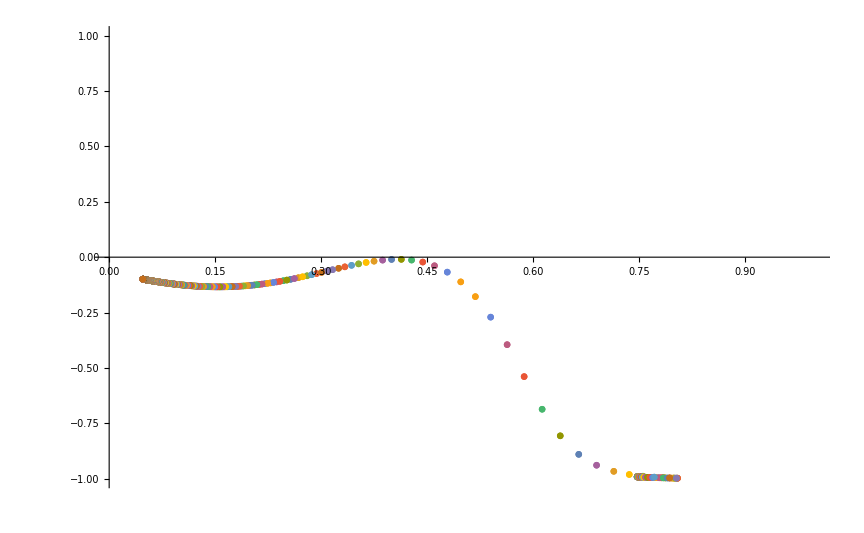

```mathematica
(*Plot each solution for each initial condition*)
EinsteinPlotLimitingCompact=ListPlot[EinsteinPointSolutionsLimitingCompact,PlotRange->{{0,1},{-1,1}}]
```

#### Plot the X-Y-Z Phase Space

```mathematica
KMaxLimitingCompact=K/.Solve[Y0Limiting==0,K][[1]]
```

0.0356667

```mathematica
solLimitingCompact[1]=trajLimitingCompact[KDensityParametersOpen]
solLimitingCompact[2]=trajLimitingCompact[KDensityParametersClosed]
solLimitingCompact[3]=trajLimitingCompact[-.1]
solLimitingCompact[4]=trajLimitingCompact[KMaxLimitingCompact]
solLimitingCompact[5]=trajLimitingCompact[0.005]
```

NDSolve::mxst: Maximum number of 134831 steps reached at the point t == -8.88046.

{{X1→InterpolatingFunction[{{-8.88046, 100.}}, <>],Y1→InterpolatingFunction[{{-8.88046, 100.}}, <>],Z1→InterpolatingFunction[{{-8.88046, 100.}}, <>]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

Power::infy: Infinite expression 1/(√(0.+0. ⅈ)) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate,0.+0. ⅈ,Indeterminate} is not a list of numbers with dimensions {3} at {t,X1[t],Y1[t],Z1[t]} = {-2.88294,0.75+0. ⅈ,1.+0. ⅈ,0.42446+0. ⅈ}.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
trajLimitingCompactXYZ[1]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompact[1],{t,-8.58,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZ[2]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompact[2],{t,-100,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZ[3]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompact[3],{t,-2.87,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZ[4]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompact[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCompactXYZ[5]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solLimitingCompact[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajLimitingCaseCompact=Table[trajLimitingCompactXYZ[i],{i,1,5}];
```

```mathematica
EinsteinFixedPointsLimitingCompact=ListPointPlot3D[{EinsteinPointLimitingCompact},PlotStyle->Black];
```

```mathematica
CFSLimitingSolCompact=NDSolve[{deXt,deYt,deZt,X1[0]==EinsteinPointLimitingCompact[[1]],Y1[0]==0,Z1[0]==EinsteinPointLimitingCompact[[3]]},{X1,Y1,Z1},{t,-100,100}]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
CFSLimitingCompact=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.CFSLimitingSolCompact,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
FFSLimitingSolCompact=trajLimitingCompact[0]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
FFSLimitingCompact=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.FFSLimitingSolCompact,{t,-10,100},PlotStyle -> {{Darker[Green],Thick}}],PlotPoints->500,PlotRange->{{0,1},{-1,1},{0,1}}];
```

```mathematica
(*FFSLimiting=Plot3D[{Sqrt[x/3+z/3],-Sqrt[x/3+z/3]},{x,0,6},{z,0,4},Mesh->None,PlotStyle->{{Darker[Green],Opacity[0.25]}}]*)
```

```mathematica
Show[trajLimitingCaseCompact,EinsteinFixedPointsLimitingCompact,CFSLimitingCompact,FFSLimitingCompact,AccnXYZ,FPsXYZ,CompactFPShowXYZ,PlotRange->{{0,1},{-1,1},{0,1}},AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

#### Plot the X-Z Projection

```mathematica
trajLimitingCompactXZ=ParametricPlot[Evaluate[{{X1[t],Z1[t]}}/.solLimitingCompact[1],{t,-8.58,100},PlotStyle -> {{Black, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
EinsteinFixedPointsLimitingCompactXZ=ListPlot[{{EinsteinPointLimitingCompact[[1]],EinsteinPointLimitingCompact[[3]]}},PlotStyle->Black];
```

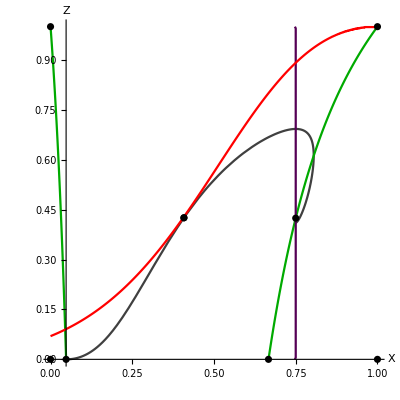

```mathematica
Show[trajLimitingCompactXZ,XLine,ZLine,AccnXZ,EinsteinFixedPointsLimitingCompactXZ,FPsXZ,CompactFPShowXZ,PlotRange->{{0,1},{0,1}},AxesLabel->{"X","Z"}]
```

### Two Einstein Fixed Points

#### Find the Einstein Fixed Points

```mathematica
(*Fix z0 using the density parameters*)
z0TwoEinsteinPoints=Ωm0*ℛ/(Ωx0*α);
```

```mathematica
(*Compactify z0*)
Z0TwoEinsteinPoints=z0TwoEinsteinPoints/(1+z0TwoEinsteinPoints)
```

0.0432077

```mathematica
(*Substitute Z0TwoEinsteinPoints into Y0 for this case*)
Y0TwoEinsteinPoints=Y0/.Z0->Z0TwoEinsteinPoints
```

(√(0.0483863-K))/(√(1.04839-K))

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajTwoEinsteinPointsCompact[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0TwoEinsteinPoints,Z1[0]==Z0TwoEinsteinPoints},{X1,Y1,Z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (√(0.0483863-1. K))/(√(1.04839-1. K)) is not a number or a rectangular array of numbers.

NDSolve[{X1'[t]==-(3 (0.5 (1-X1[t])-0.25 X1[t]) (-0.05 (1-X1[t])+X1[t]) Y1[t])/(√(1-Y1[t]^2))-((1-X1[t]) X1[t] Y1[t] Z1[t])/(√(1-Y1[t]^2) (1-Z1[t])),Y1'[t]==-Y1[t]^2 √(1-Y1[t]^2)-1/6 (1-Y1[t]^2)^(3/2) (-0.075-(0.4625 X1[t])/(1-X1[t])-(0.75 X1[t]^2)/(1-X1[t])^2+Z1[t]/(1-Z1[t])),Z1'[t]==-(3 Y1[t] (1-Z1[t]) Z1[t])/(√(1-Y1[t]^2))+(X1[t] Y1[t] (1-Z1[t]) Z1[t])/((1-X1[t]) √(1-Y1[t]^2)),X1[0]==0.0909091,Y1[0]==(√(0.0483863-K))/(√(1.04839-K)),Z1[0]==0.0432077},{X1,Y1,Z1},{t,-100,100}]

```mathematica
XTableSol1TwoEinsteinPointsCompact=Table[X1[i]/.trajTwoEinsteinPointsCompact[0],{i,-2,100,.01}];
YTableSol1TwoEinsteinPointsCompact=Table[Y1[i]/.trajTwoEinsteinPointsCompact[0],{i,-2,100,.01}];
ZTableSol1TwoEinsteinPointsCompact=Table[Z1[i]/.trajTwoEinsteinPointsCompact[0],{i,-2,100,.01}];
```

```mathematica
(*Using the values of x and z found numerically, solve the equation to find the Einstein fixed points*)
EinsteinPlotValuesSol1TwoEinsteinPointsCompact=(ZTableSol1TwoEinsteinPointsCompact/(1-ZTableSol1TwoEinsteinPointsCompact))+(XTableSol1TwoEinsteinPointsCompact/(1-XTableSol1TwoEinsteinPointsCompact))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSol1TwoEinsteinPointsCompact/(1-XTableSol1TwoEinsteinPointsCompact))^2;
```

```mathematica
NearestToZeroTwoEinsteinPoints1Compact=Flatten[Nearest[EinsteinPlotValuesSol1TwoEinsteinPointsCompact,0]]
```

{0.00021485}

```mathematica
PositionNearestToZeroTwoEinsteinPoints1Compact=Flatten[Position[EinsteinPlotValuesSol1TwoEinsteinPointsCompact,NearestToZeroTwoEinsteinPoints1Compact]]
```

{32}

```mathematica
EinsteinPoint1TwoEinsteinPointsCompact=Flatten[{XTableSol1TwoEinsteinPointsCompact[[PositionNearestToZeroTwoEinsteinPoints1Compact]],0,ZTableSol1TwoEinsteinPointsCompact[[PositionNearestToZeroTwoEinsteinPoints1Compact]]}]
```

{0.130255,0,0.138897}

```mathematica
(*Table of all x1 and z1 values for each solution for each value of t*)
XTableSol2TwoEinsteinPointsCompact=Table[X1[i]/.trajTwoEinsteinPointsCompact[0],{i,-5.6,-3.2,.001}];
YTableSol2TwoEinsteinPointsCompact=Table[Y1[i]/.trajTwoEinsteinPointsCompact[0],{i,-5.6,-3.2,.001}];
ZTableSol2TwoEinsteinPointsCompact=Table[Z1[i]/.trajTwoEinsteinPointsCompact[0],{i,-5.6,-3.2,.001}];
```

```mathematica
(*Using the values of x and z found numerically, solve the equation to find the Einstein fixed points*)
EinsteinPlotValuesSol2TwoEinsteinPointsCompact=(ZTableSol2TwoEinsteinPointsCompact/(1-ZTableSol2TwoEinsteinPointsCompact))+(XTableSol2TwoEinsteinPointsCompact/(1-XTableSol2TwoEinsteinPointsCompact))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSol2TwoEinsteinPointsCompact/(1-XTableSol2TwoEinsteinPointsCompact))^2;
```

```mathematica
NearestToZeroTwoEinsteinPoints2Compact=Flatten[Nearest[EinsteinPlotValuesSol2TwoEinsteinPointsCompact,0]]
```

{0.00312607}

```mathematica
PositionNearestToZeroTwoEinsteinPoints2Compact=Flatten[Position[EinsteinPlotValuesSol2TwoEinsteinPointsCompact,NearestToZeroTwoEinsteinPoints2Compact]]
```

{1876}

```mathematica
EinsteinPoint2TwoEinsteinPointsCompact=Flatten[{XTableSol2TwoEinsteinPointsCompact[[PositionNearestToZeroTwoEinsteinPoints2Compact]],0,ZTableSol2TwoEinsteinPointsCompact[[PositionNearestToZeroTwoEinsteinPoints2Compact]]}]
```

{0.633296,0,0.756912}

```mathematica
(*Put the Einstein fixed points into a common variable name*)
EinsteinPointTwoEPtsCompact[1]=EinsteinPoint1TwoEinsteinPointsCompact;
EinsteinPointTwoEPtsCompact[2]=EinsteinPoint2TwoEinsteinPointsCompact;
```

```mathematica
(*Put the Einstein fixed points into a table*)
EinsteinPointsTwoEPtsCompact=Table[EinsteinPointTwoEPtsCompact[i],{i,1,2}];
```

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
EinsteinPointTableTwoEinsteinPointsCompact=Table[{EinsteinPointsTwoEPtsCompact[[i]]//MatrixForm,Simplify[JCompactXYZ/.{X->EinsteinPointsTwoEPtsCompact[[i,1]],Y->EinsteinPointsTwoEPtsCompact[[i,2]],Z->EinsteinPointsTwoEPtsCompact[[i,3]]}]//MatrixForm,Eigenvalues[JCompactXYZ/.{X->EinsteinPointsTwoEPtsCompact[[i,1]],Y->EinsteinPointsTwoEPtsCompact[[i,2]],Z->EinsteinPointsTwoEPtsCompact[[i,3]]}]//MatrixForm,Eigenvectors[JCompactXYZ/.{X->EinsteinPointsTwoEPtsCompact[[i,1]],Y->EinsteinPointsTwoEPtsCompact[[i,2]],Z->EinsteinPointsTwoEPtsCompact[[i,3]]}]//MatrixForm},{i,1,2}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTableTwoEinsteinPointsCompact=TableForm[EinsteinPointTableTwoEinsteinPointsCompact,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues","Eigenvectors"}}]
```

Fixed Point | Jacobian | Eigenvalues | Eigenvectors
(0.130255
0
0.138897) | (0. | -0.122997 | 0.
0.151396 | 0. | -0.22477
0. | -0.340903 | 0.) | (-0.240839
0.240839
6.38968×10^-18) | (-0.28266 | -0.553477 | -0.783433
0.28266 | -0.553477 | 0.783433
0.829403 | -5.09251×10^-17 | 0.55865)
(0.633296
0
0.756912) | (0. | -0.769284 | 0.
3.78391 | 0. | -2.82047
0. | -0.234229 | 0.) | (-1.00153×10^-17+1.50009 ⅈ
-1.00153×10^-17-1.50009 ⅈ
5.82828×10^-17+0. ⅈ) | (-3.46579×10^-16-0.451978 ⅈ | -0.88135+0. ⅈ | -1.25865×10^-16-0.137617 ⅈ
-3.46579×10^-16+0.451978 ⅈ | -0.88135+0. ⅈ | -1.25865×10^-16+0.137617 ⅈ
0.597629+0. ⅈ | 1.24466×10^-15+0. ⅈ | 0.801773+0. ⅈ)

```mathematica
(*Table of all x1 and z1 values for each solution for each value of t*)
XTableSolTwoEinsteinPointsFullCompact=Table[X1[i]/.trajTwoEinsteinPointsCompact[0],{i,-100,100,.1}];
YTableSolTwoEinsteinPointsFullCompact=Table[Y1[i]/.trajTwoEinsteinPointsCompact[0],{i,-100,100,.1}];
ZTableSolTwoEinsteinPointsFullCompact=Table[Z1[i]/.trajTwoEinsteinPointsCompact[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the equation to find the Einstein fixed points*)
EinsteinPlotValuesSolTwoEinsteinPointsFullXZ=(ZTableSolTwoEinsteinPointsFullCompact/(1-ZTableSolTwoEinsteinPointsFullCompact))+(XTableSolTwoEinsteinPointsFullCompact/(1-XTableSolTwoEinsteinPointsFullCompact))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolTwoEinsteinPointsFullCompact/(1-XTableSolTwoEinsteinPointsFullCompact))^2;
```

```mathematica
EinsteinPlotValuesSolTwoEinsteinPointsFullCompact=EinsteinPlotValuesSolTwoEinsteinPointsFullXZ/Sqrt[1+EinsteinPlotValuesSolTwoEinsteinPointsFullXZ^2];
```

```mathematica
(*Merge the xTable values and the EinsteinPlotValueSol values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsTwoEinsteinPointsCompact=MapThread[h,{XTableSolTwoEinsteinPointsFullCompact,EinsteinPlotValuesSolTwoEinsteinPointsFullCompact}];
```

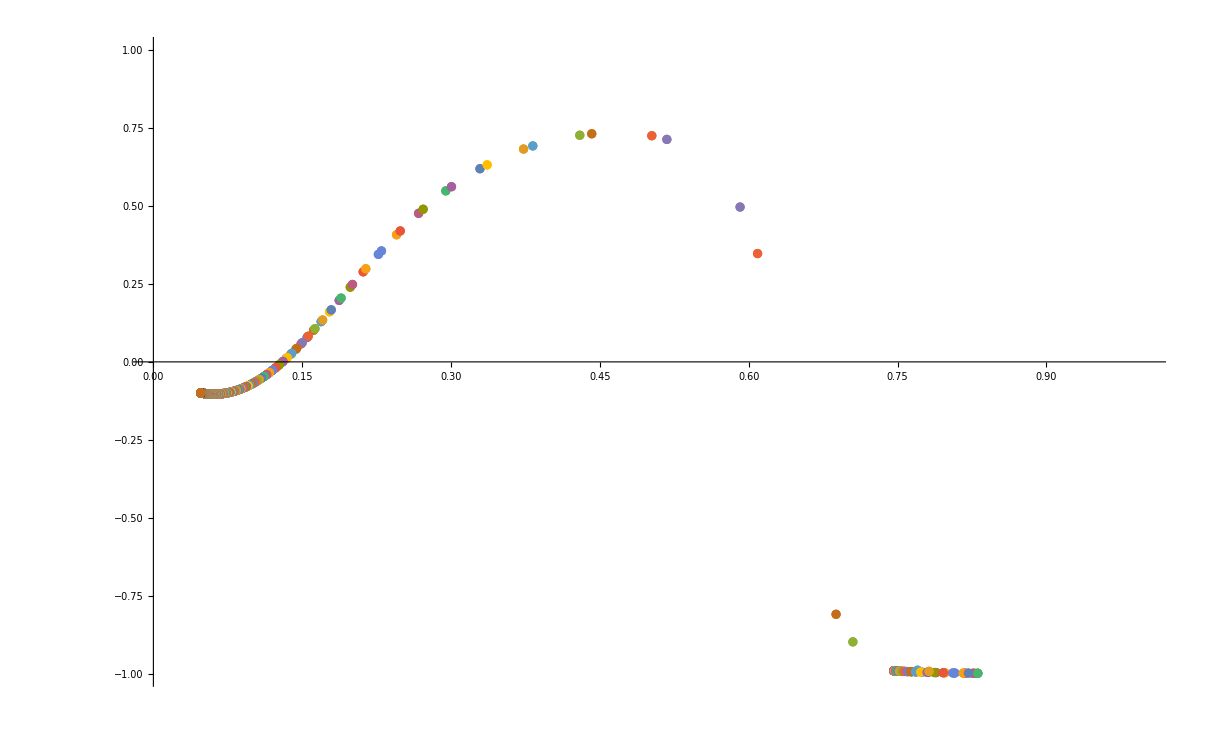

```mathematica
(*Plot each solution for each initial condition*)
EinsteinPlotTwoEinsteinPointsCompact=ListPlot[EinsteinPointSolutionsTwoEinsteinPointsCompact,PlotRange->{{0,1},{-1,1}}]
```

#### Plot the X-Y-Z Phase Space

```mathematica
(*Find the maximum value of K so that y0 is not imaginary*)
KMaxTwoEinsteinPointsCompact=K/.Flatten[Solve[Y0TwoEinsteinPoints==0,K]]
```

0.0483863

```mathematica
solTwoEinsteinPointsCompact[1]=trajTwoEinsteinPointsCompact[KDensityParametersOpen]
```

NDSolve::mxst: Maximum number of 238904 steps reached at the point t == -7.0047.

{{X1→InterpolatingFunction[{{-7.0047, 100.}}, <>],Y1→InterpolatingFunction[{{-7.0047, 100.}}, <>],Z1→InterpolatingFunction[{{-7.0047, 100.}}, <>]}}

```mathematica
solTwoEinsteinPointsCompact[2]=trajTwoEinsteinPointsCompact[KDensityParametersClosed]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsCompact[3]=trajTwoEinsteinPointsCompact[-.1]
```

NDSolve::ndcf: Repeated convergence test failure at t == -2.6552; unable to continue.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsCompact[4]=trajTwoEinsteinPointsCompact[KMaxTwoEinsteinPointsCompact]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
solTwoEinsteinPointsCompact[5]=trajTwoEinsteinPointsCompact[0.005]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
trajTwoEinsteinPointsCompactXYZ[1]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompact[1],{t,-6.67,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsCompactXYZ[2]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompact[2],{t,-100,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsCompactXYZ[3]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompact[3],{t,-2.65,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsCompactXYZ[4]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompact[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75],Dashed}}],PlotPoints->500,PlotRange->Full];
```

```mathematica
trajTwoEinsteinPointsCompactXYZ[5]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solTwoEinsteinPointsCompact[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajTwoEinsteinPointsCaseCompact=Table[trajTwoEinsteinPointsCompactXYZ[i],{i,1,5}];
```

```mathematica
EinsteinFixedPointsTwoEinsteinPointsCompact=ListPointPlot3D[{EinsteinPoint1TwoEinsteinPointsCompact,EinsteinPoint2TwoEinsteinPointsCompact},PlotStyle->Black];
```

```mathematica
CFSTwoEinsteinPointsSolCompact=NDSolve[{deXt,deYt,deZt,X1[0]==EinsteinPoint1TwoEinsteinPointsCompact[[1]],Y1[0]==-0.0005,Z1[0]==EinsteinPoint1TwoEinsteinPointsCompact[[3]]},{X1,Y1,Z1},{t,-100,100}]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
CFSTwoEinsteinPointsCompact=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.CFSTwoEinsteinPointsSolCompact,{t,-6.67,100},PlotStyle -> {{Black}}],PlotPoints->500,PlotRange->All];
```

```mathematica
FFSTwoEinsteinPointsSolCompact=trajTwoEinsteinPointsCompact[0]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
FFSTwoEinsteinPointsCompact=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.FFSTwoEinsteinPointsSolCompact,{t,-8,100},PlotStyle -> {{Darker[Green],Thick}}],PlotPoints->500,PlotRange->{{0,6},{-3,3},{0,6}}];
```

```mathematica
Show[trajTwoEinsteinPointsCaseCompact,CFSTwoEinsteinPointsCompact,EinsteinFixedPointsTwoEinsteinPointsCompact,FFSTwoEinsteinPointsCompact,AccnXYZ,FPsXYZ,CompactFPShowXYZ,PlotRange->{{0,1},{-1,1},{0,1}},AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

#### Plot the X-Z Projection

```mathematica
trajTwoEinsteinPointsCompactXZ=ParametricPlot[Evaluate[{{X1[t],Z1[t]}}/.solTwoEinsteinPointsCompact[1],{t,-6.67,100},PlotStyle -> {{Black, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
EinsteinFixedPointsTwoEinsteinPointsCompactXZ=ListPlot[{{EinsteinPoint1TwoEinsteinPointsCompact[[1]],EinsteinPoint1TwoEinsteinPointsCompact[[3]]},{EinsteinPoint2TwoEinsteinPointsCompact[[1]],EinsteinPoint2TwoEinsteinPointsCompact[[3]]}},PlotStyle->Black];
```

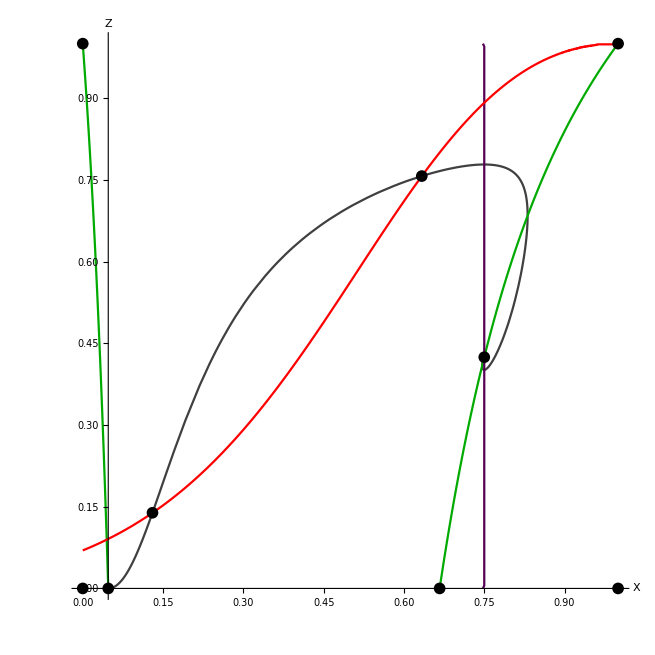

```mathematica
Show[trajTwoEinsteinPointsCompactXZ,XLine,ZLine,AccnXZ,EinsteinFixedPointsTwoEinsteinPointsCompactXZ,FPsXZ,CompactFPShowXZ,PlotRange->{{0,1},{0,1}},AxesLabel->{"X","Z"}]
```

### No Einstein Fixed Points

#### Plot to show there are no Einstein fixed points

```mathematica
(*Fix z0 such that there are no Einstein fixed points on the surface*)
z0NoEinsteinPoints=0.005;
```

```mathematica
(*Compactify z0*)
Z0NoEinsteinPoints=z0NoEinsteinPoints/(1+z0NoEinsteinPoints)
```

0.00497512

```mathematica
(*Substitute Z0NoEinsteinPoints into Y0 for this case*)
Y0NoEinsteinPoints=Y0/.Z0->Z0NoEinsteinPoints
```

(√(0.035-K))/(√(1.035-K))

```mathematica
(*Numerically solve the system of equations using the initial conditions defined above*)
trajNoEinsteinPointsCompact[K_]=NDSolve[{deXt,deYt,deZt,X1[0]==X0,Y1[0]==Y0NoEinsteinPoints,Z1[0]==Z0NoEinsteinPoints},{X1,Y1,Z1},{t,-100,100}]
```

NDSolve::ndinnt: Initial condition (√(0.035-1. K))/(√(1.035-1. K)) is not a number or a rectangular array of numbers.

NDSolve[{X1'[t]==-(3 (0.5 (1-X1[t])-0.25 X1[t]) (-0.05 (1-X1[t])+X1[t]) Y1[t])/(√(1-Y1[t]^2))-((1-X1[t]) X1[t] Y1[t] Z1[t])/(√(1-Y1[t]^2) (1-Z1[t])),Y1'[t]==-Y1[t]^2 √(1-Y1[t]^2)-1/6 (1-Y1[t]^2)^(3/2) (-0.075-(0.4625 X1[t])/(1-X1[t])-(0.75 X1[t]^2)/(1-X1[t])^2+Z1[t]/(1-Z1[t])),Z1'[t]==-(3 Y1[t] (1-Z1[t]) Z1[t])/(√(1-Y1[t]^2))+(X1[t] Y1[t] (1-Z1[t]) Z1[t])/((1-X1[t]) √(1-Y1[t]^2)),X1[0]==0.0909091,Y1[0]==(√(0.035-K))/(√(1.035-K)),Z1[0]==0.00497512},{X1,Y1,Z1},{t,-100,100}]

```mathematica
(*Table of all x1 and z1 values for each solution for each value of t*)
XTableSolNoEinsteinPointsFullCompact=Table[X1[i]/.trajNoEinsteinPointsCompact[0],{i,-100,100,.1}];
YTableSolNoEinsteinPointsFullCompact=Table[Y1[i]/.trajNoEinsteinPointsCompact[0],{i,-100,100,.1}];
ZTableSolNoEinsteinPointsFullCompact=Table[Z1[i]/.trajNoEinsteinPointsCompact[0],{i,-100,100,.1}];
```

```mathematica
(*Using the values of x and z found numerically, solve the equation to find the Einstein fixed points*)
EinsteinPlotValuesSolNoEinsteinPointsFullCompact=(ZTableSolNoEinsteinPointsFullCompact/(1-ZTableSolNoEinsteinPointsFullCompact))+(XTableSolNoEinsteinPointsFullCompact/(1-XTableSolNoEinsteinPointsFullCompact))*(1+3*wx-3*ϵ*ℛ)-3*ℛ*(1+wx)+3*ϵ*(XTableSolNoEinsteinPointsFullCompact/(1-XTableSolNoEinsteinPointsFullCompact))^2;
```

```mathematica
EinsteinPlotValuesSolNoEinsteinPointsFullXZ=EinsteinPlotValuesSolNoEinsteinPointsFullCompact/Sqrt[1+EinsteinPlotValuesSolNoEinsteinPointsFullCompact^2];
```

```mathematica
(*Merge the xTable values and the EinsteinPlotValueSol values*)
h[p_,q_]:=Transpose[{p,q}];
EinsteinPointSolutionsNoEinsteinPointsCompact=MapThread[h,{XTableSolNoEinsteinPointsFullCompact,EinsteinPlotValuesSolNoEinsteinPointsFullXZ}];
```

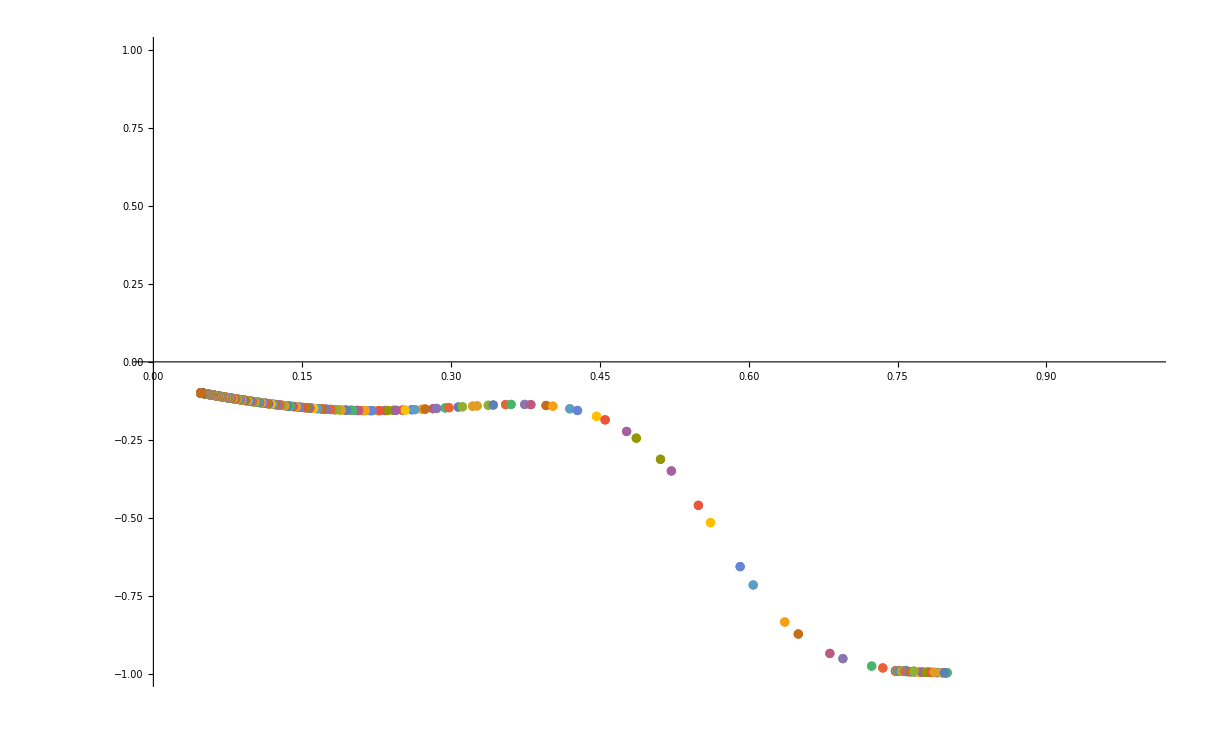

```mathematica
(*Plot each solution for each initial condition*)
EinsteinPlotNoEinsteinPointsCompact=ListPlot[EinsteinPointSolutionsNoEinsteinPointsCompact,PlotRange->{{0,1},{-1,1}}]
```

#### Plot the X-Y-Z Phase Space

```mathematica
KMaxNoEinsteinPointsCompact=K/.Solve[Y0NoEinsteinPoints==0,K][[1]]
```

0.035

```mathematica
solNoEinsteinPointsCompact[1]=trajNoEinsteinPointsCompact[KDensityParametersOpen]
solNoEinsteinPointsCompact[2]=trajNoEinsteinPointsCompact[KDensityParametersClosed]
solNoEinsteinPointsCompact[3]=trajNoEinsteinPointsCompact[-.1]
solNoEinsteinPointsCompact[4]=trajNoEinsteinPointsCompact[0.01]
solNoEinsteinPointsCompact[5]=trajNoEinsteinPointsCompact[KMaxNoEinsteinPointsCompact]
```

NDSolve::mxst: Maximum number of 131491 steps reached at the point t == -8.89343.

{{X1→InterpolatingFunction[{{-8.89343, 100.}}, <>],Y1→InterpolatingFunction[{{-8.89343, 100.}}, <>],Z1→InterpolatingFunction[{{-8.89343, 100.}}, <>]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

NDSolve::ndsz: At t == -2.89969, step size is effectively zero; singularity or stiff system suspected.

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
trajNoEinsteinPointsCompactXYZ[1]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompact[1],{t,-8.89,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZ[2]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompact[2],{t,-100,100},PlotStyle -> {{Purple, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZ[3]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompact[3],{t,-2.89,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZ[4]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompact[4],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsCompactXYZ[5]=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.solNoEinsteinPointsCompact[5],{t,-100,100},PlotStyle -> {{Gray, Opacity[0.75]}}],PlotPoints->500];
```

```mathematica
trajNoEinsteinPointsPlotsCompact=Table[trajNoEinsteinPointsCompactXYZ[i],{i,1,5}];
```

```mathematica
FFSNoEinsteinPointsSolCompact=trajNoEinsteinPointsCompact[0]
```

{{X1→InterpolatingFunction[…],Y1→InterpolatingFunction[…],Z1→InterpolatingFunction[…]}}

```mathematica
FFSNoEinsteinPointsCompact=ParametricPlot3D[Evaluate[{{X1[t],Y1[t],Z1[t]},{X1[t],-Y1[t],Z1[t]}}/.FFSNoEinsteinPointsSolCompact,{t,-10,100},PlotStyle -> {{Darker[Green],Thick}}],PlotPoints->500,PlotRange->{{0,6},{-3,3},{0,6}}];
```

```mathematica
Show[trajNoEinsteinPointsPlotsCompact,FFSNoEinsteinPointsCompact,AccnXYZ,FPsXYZ,CompactFPShowXYZ,PlotRange->{{0,1},{-1,1},{0,1}},AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

#### Plot the X-Z Projection

```mathematica
trajNoEinsteinPointsCompactXZ=ParametricPlot[Evaluate[{{X1[t],Z1[t]}}/.solNoEinsteinPointsCompact[1],{t,-8.89,100},PlotStyle -> {{Black, Opacity[0.75]}}],PlotPoints->500];
```

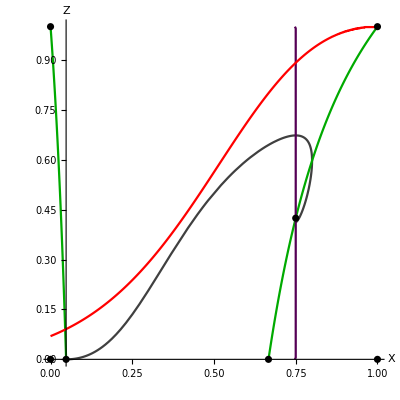

```mathematica
Show[trajNoEinsteinPointsCompactXZ,XLine,ZLine,AccnXZ,FPsXZ,CompactFPShowXZ,PlotRange->{{0,1},{0,1}},AxesLabel->{"X","Z"}]
```